## Taylor

```mathematica
Taylor[f_,x_,x0_,r_]:=
Module[{n,m,v,c,g,h,l,fac,pr,dein,ap,de,sost},
n=Length[x];
m=Join[Table[in[i],{i,1,n}],{0}];
v1=Table[{m[[i]]-m[[i+1]]},{i,1,n}]//Flatten;
v=Table[{m[[i]],0,c[i]},{i,1,n}];
c[1]=r;
c[i_]:=m[[i-1]]/;i>1;
g[w1_,{z1__}]:=Flatten[Table[w1,z1],n-1];
h=g[v1,v];
l=Length[h];
fac[i_]:=Product[
Factorial[h[[i,j]]],
{j,1,Length[h[[i]]]}];
pr[i_]:=Product[(x[[j]]-x0[[j]])^h[[i,j]],{j,1,n}];
dein[i_]:=Table[{x[[j]],h[[i,j]]},{j,1,n}];
ap[{q__}]:=q;
de[i_]:=D[f,ap[dein[i]]];
sost=Table[x[[i]]->x0[[i]],{i,1,n}];
tay=Sum[(1/fac[i])*(de[i]/.sost)*pr[i],{i,1,l}];
]

Taylor1[f_,var_,var0_,r_]:=
Module[{},
n=Length[var];
m=Table[var[[i]]->var0[[i]],{i,1,n}];
ind=Join[Table[j[i],{i,1,n}],{0}];
de[0]=f;
de[i_]:=1/((ind[[i]]-ind[[i+1]])!)*D[de[i-1],{var[[i]],ind[[i]]-ind[[i+1]]}];
g[{w__}]:=Sum[(de[n]/.m)*Product[(var[[i]]-var0[[i]])^(ind[[i]]-ind[[i+1]]),{i,1,n}],w];
h=Join[{{ind[[1]],0,r}},Table[{ind[[i]],0,ind[[i-1]]},{i,2,n}]];

g[h];
Print[g[h]]
]
```

```mathematica
"F:\\Ottica\\OptFin\\Programmidefin\\Aberr\\TotalAberrations.nb"
```

# Total Aberrations

```mathematica
Off[General::spell1]
Off[General::spell]
Off[∞::indet]
Off[Power::infy]
Off[Simplify::infd]

TotalAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,option1_]:=
Module[{},
(* number of surfaces and wave lengths *)
n=Length[rad];
m=Length[waves];

(* Distances among the surfaces *)
thicke=Reverse[Take[thick,{1,nstop-1}]];
thicke1=Join[thicke,{0}];
rade=-Reverse[Take[rad,{1,nstop}]]//Flatten;

(* Evaluation of the aperture stop images supplied by the surfaces preceeding the stop:
the last one is the entrance pupil. *)
Do[
inde[h]=Reverse[Take[ind[[h]],{1,nstop}]];
inde1[h]=Prepend[inde[h],1],
{h,1,m}];


Do[
ze[h,1]=If[nstop===0,dis,-dis],
{h,1,3}];

Do[
Do[
Qe[h,i]=(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rade[[i]]-(inde1[h][[i+1]])/w1[h,i]+(inde1[h][[i+1]])/rade[[i]];
ze1[h,i]=Which[ze[h,i]===0,ze[h,i],ze[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,ze[h,i]=!=-Infinity&&Simplify[Numerator[Together[(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rad[[i]]+(inde1[h][[i+1]])/rad[[i]]]]]===0,-Infinity,ze[h,i]=!=-Infinity||ze[h,i]===-Infinity,Solve[Qe[h,i]==0,w1[h,i]][[1,1,2]]]; ze[h,i+1]=ze1[h,i]-thicke1[[i]],
{i,1,nstop}],
{h,1,m}];
Do[
de[h]=Which[nstop===0,dis,nstop=!=0,-ze1[h,nstop]],
{h,1,3}];

If[option1==1,Print["Distance of entrance pupil from the first surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_e = ", de[1](*//Simplify*)]];

Do[
ye[h,1]=stoprad;
Do[
ye1[h,i]=If[ze[h,i]=!=0,(inde1[h][[i]] ze1[h,i])/(inde1[h][[i+1]] ze[h,i])ye[h,i],ye[h,i]];
ye[h,i+1]=ye1[h,i],
{i,1,nstop}];
diame[h]=Which[nstop===0,stoprad,nstop=!=0,ye1[h,nstop]],
{h,1,m}];

If[option1==1,Print["Radius of entrance pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_en = ",diame[1]]];

(* Evaluation of exit pupil *)
thick2=Join[thick,{0}];
Do[
zee[h,1]=de[h];
Do[zee1[h,i]=Which[zee[h,i]===0,0,zee[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,zee[h,i]=!=-Infinity&&ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]+ind[[h,i+1]]/rad[[i]]===0,-Infinity,zee[h,i]=!=-Infinity||zee[h,i]===-Infinity,Solve[Numerator[Together[ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]-ind[[h,i+1]]/fe1[h,i]+ind[[h,i+1]]/rad[[i]]]]==0,fe1[h,i]][[1]][[1,2]]];zee[h,i+1]=zee1[h,i]-thick2[[i]],
{i,1,n}],{h,1,m}];

If[option1==1,Print["Distance of the exit pupil from the last surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_(e, n) = ",zee1[1,n](*//Simplify*)]];

Do[
yee[h,1]=diame[h];
Do[
yee1[h,i]=Which[zee[h,i]=!=0,(ind[[h,i]] zee1[h,i])/(ind[[h,i+1]] zee[h,i])yee[h,i],zee[h,i]===0,yee[h,i]];
yee[h,i+1]=yee1[h,i],{i,1,n}],
{h,1,m}];

If[option1==1,Print["Radius of exit pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_ex = ",Abs[ yee1[1,n]]]];

(* Pupil Magnification  *)

Do[
Do[
Mae[h,i]=yee1[h,i]/yee[h,1],
{i,1,n}],
{h,1,m}];

(*Principal planes and focal length*)
Do[
Do[P[h,i]=(ind[[h,i+1]]-ind[[h,i]])/rad[[i]];
R0[h,i]={{1,0},{(-P[h,i])/ind[[h,i+1]],ind[[h,i]]/ind[[h,i+1]]}},
{i,1,n}],
{h,1,m}];


If[n==1,Goto[1],Goto[2]];

Label[1];
Do[Mt[h]=R0[h,1],{h,1,m}];

Goto[3];

Label[2];
(*Total matrix of the i-th surface*)

Do[D0[i]={{1,thick[[i]]},{0,1}},{i,1,n-1}];
Do[
Do[
B0[h,i]=If[i<n,D0[i].R0[h,i],R0[h,n]],{i,1,n}],{h,1,m}];

(*Matrices of the sub-systems*)
Do[
Do[
b[h,1]=B0[h,1];
b[h,i]=B0[h,i].b[h,i-1],
{i,2,n}],{h,1,m}];

(*Total matrix of the system*)
Do[Mt[h]=b[h,n],{h,1,m}];
Label[3];


(*Distances of the principal planes from the first and last surface, respectively*)


Do[
zp[h]=If[Mt[h][[2,1]]===0,0,1/(Mt[h][[2,1]])(Mt[h][[1,2]]Mt[h][[2,1]]+Mt[h][[2,2]]-Mt[h][[1,1]]Mt[h][[2,2]])];
z1p[h]=If[Mt[h][[2,1]]===0,0,(1-Mt[h][[1,1]])/(Mt[h][[2,1]])],{h,1,m}];
(***********************************)
If[option1===1,Print["Distance of the first principal plane from the first surface = ",zp[1]]];
If[option1===1,Print["Distance of the second principal plane from the last surface = ",z1p[1]]];

(* Distances of the images *)


Do[zog[h,1]=dobject,{h,1,m}];

Do[
Do[zog1[h,i]=Which[rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])],

rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zog[h,i]=!=-Infinity,(ind[[h,i+1]]zog[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zog[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zog[h,i]===-Infinity,-Infinity];zog[h,i+1]=zog1[h,i]-thick2[[i]],{i,1,n}],{h,1,m}];
If[option1==1,Print["Gaussian distances of the images from the surfaces for λ = ",waves[[1]]]];
If[option1==1,Print[Table[zog1[1,i],{i,1,n}]]];

(*Focal length *)
Do[zoginf[h,1]=-Infinity,{h,1,m}];
Do[
Do[zog1inf[h,i]=Which[rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])],

rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zoginf[h,i]=!=-Infinity,(ind[[h,i+1]]zoginf[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zoginf[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zoginf[h,i]===-Infinity,-Infinity];zoginf[h,i+1]=zog1inf[h,i]-thick2[[i]],{i,1,n}];,{h,1,m}];
Do[foc[h]=zog1inf[h,n]-z1p[h],{h,1,m}];
If[option1===1, Print["Focal length = ",foc[1]]];
(*
dinf=Cases[rad,Infinity];
If[Length[dinf]>0,Goto[lab]];
*)
(*Height of images *)
Do[hobj1[h,1]=If[dobject===-Infinity,(ind[[h,1]] zog1[h,1])/ind[[h,2]] π/180 angle,(ind[[h,1]] zog1[h,1])/(ind[[h,2]]zog[h,1])hobject],{h,1,m}];
Do[Do[hobj[h,i]=hobj1[h,i-1];hobj1[h,i]=(ind[[h,i]] zog1[h,i])/(ind[[h,i+1]]zog[h,i])hobj[h,i] ,{i,2,n}],{h,1,m}];


If[option1==1,Print["Image height = ",hobj1[1,n]]];

Label[lab];
(*Aberrations *)


Do[
Do[
C1[h,i]=If[Length[costasf[[i]]]==2,-costasf[[i,1]](ind[[h,i+1]]-ind[[h,i]])-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2,-costasf[[i]](ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2],
{i,1,n}],
{h,1,m}];

(*Coefficients of coma for stop on the surface*)
Do[
Do[
C2[h,i]=ind[[h,i]]^2/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]]),
{i,1,n}],
{h,1,m}];


(* Coefficients of fields curvature and astigmatism for stop on the surface *)

Do[
Do[
C3[h,i]=ind[[h,i]]/4(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2(1/zog[h,i]-1/rad[[i]]);
C4[h,i]=(-ind[[h,i]]^2)/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))+C3[h,i],
{i,1,n}],
{h,1,m}];

(*Coefficients of distorsion for stop on the surface *)

Do[
Do[
C5[h,i]=-ind[[h,i]]/2(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2,
{i,1,n}],
{h,1,m}];


(* Aberration Coefficients depending on the stop position *)

Do[
Do[
c1[h,i]=If[zog[h,i]===-Infinity,1,zog[h,i]/(zog[h,i]-zee[h,i])];
d1[h,i]=If[zog[h,i]===-Infinity,0,zee[h,i]/(zog[h,i]-zee[h,i])];
k1[h,i]=If[zog[h,i]===-Infinity,zee[h,i],zog[h,i] d1[h,i]];
Cd1[h,i]=c1[h,i]^4 C1[h,i];
Cd2[h,i]=c1[h,i]^2(C2[h,i]-4k1[h,i]C1[h,i]);
Cd3[h,i]=(C3[h,i]-k1[h,i]C2[h,i]+2 k1[h,i]^2 C1[h,i]);
Cd4[h,i]=(C4[h,i]-3k1[h,i]C2[h,i]+6 k1[h,i]^2 C1[h,i]);
Cd5[h,i]=1/c1[h,i]^2(C5[h,i]-2k1[h,i]C4[h,i]+3 k1[h,i]^2 C2[h,i]-4 k1[h,i]^3 C1[h,i]),
{i,1,n}],
{h,1,m}];


(*Compound system*)
(* Field angle *)
Do[
theta[h]=If[dobject===-Infinity,π/180 angle,hobject/(dobject-zee[h,1])],
{h,1,m}];

(*Total spherical aberration *)

Do[
Do[
Absfer[h,i]=If[i==1,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,1] yee[h,1]^3,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,i] Mae[h,i-1]^4 yee[h,1]^3],
{i,1,n}],{h,1,m}];

Do[
Seidsphe[h]=(Cd1[h,1]+Sum[Cd1[h,i] Mae[h,i-1]^4,{i,2,n}]),
{h,1,m}];
If[option1==0,Print["Spherical coefficient"]];
If[option1==0,Print[Simplify[Seidsphe[1]]]];
Do[Absftot[h]=Sum[Absfer[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Do[Print["Total spherical aberration = ",Simplify[Absftot[h]],"    ( λ = ",waves[[h]]," )"], {h,1,m}]];

(*Total sagittal coma *)
Do[Comapar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd2[h,1] theta[1](yee[h,1])^2,{h,1,m}];

Do[Comapar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i] theta[h](yee[h,1])^2,{i,2,n},{h,1,m}];
Do[Seidcoma[h]=Cd2[h,1]+Sum[ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i],{i,2,n}],{h,1,m}];


If[option1==0,Print["Coma coefficient "]];
If[option1==0,Print[Simplify[Seidcoma[1]]]];
Do[ Comatot[h] =Sum[Comapar[h,i],{i,1,n}],{h,1,m}];

If[option1==1,Do[Print["Total coma  = ",Simplify[Comatot[h]], "   ( λ = ",waves[[h]], " )"], {h,1,m}]];




(* Astigmatism *)
Do[Astpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](Cd4[h,1]-Cd3[h,1]) (theta[h])^2 yee[h,1],{h,1,m}];

Do[
Astpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]) (theta[h])^2 yee[h,1],
{i,2,n},{h,1,m}];

Do[Seidast[h]=Sum[(ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]),{i,1,n}],{h,1,m}];

If[option1==0,Print["Astigmatism coefficient = ",Simplify[Seidast[1]]]];


Do[Asttot[h] =Sum[Astpar[h,i],{i,1,n}],{h,1,m}];


If[option1==1,Do[Print["Total astigmatism  = ",Simplify[Asttot[h]], "     ( λ = ",waves[[h]]," )"],{h,1,m}]];

Do[
Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),
{i,1,n},{h,1,m}];
Do[Seidcurv[h]= Sum[ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2, {i,1,n}],{h,1,m}];
Do[Curvpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]]^2 ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2 theta[h]^2 yee[h,1],{i,1,n},{h,1,m}];


Do[Curvtot[h]=Sum[Curvpar[h,i],{i,1,n}],
{h,1,m}];
If[option1==1,Print["Total curvature = ", Curvtot[1]]];

Do[
Do[Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),{i,1,n}],
{h,1,m}];
Do[Petzval[h]=1/Sum[Sp[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Print["Petzval radius = ", Petzval[1]]];


(* Distorsion *)
Do[
Distpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd5[h,1] theta[h]^3,{h,1,m}];
Do[
Distpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2 theta[h]^3 ,
{i,2,n},{h,1,m}];
Do[Seiddist[h] =1/Mae[h,n] Cd5[h,1]+Sum[1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2,{i,2,n}],
{h,1,m}];
Do[Disttot[h]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] Seiddist[h] theta[h]^3,{h,1,m}];
If[option1==1,Print["Total distorsion = ",Simplify[Disttot[1]]]];


]
```

# Higher-Order Aberrations

```mathematica
(*Off[FindRoot::lstol]*)

HOrdAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{},
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];



(* Evaluation of aberrations *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])(x^2+y^2) +costasf[[j]][[1]](x^2+y^2)^2,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* In the sequel, the index p denotes an object point on the Oy axis, whereas k,j fix the coordinates of the points in the entrance pupil. Finally, i denotes the i-th surface of the optical system. *)

nr=3;
div=2;

(* Points in the entrance pupil*)
Do[Do[r[h,k]=k diame[h]/10;ϕ[j]=j π/4,{k,0,nr},{j,-1,1}],{h,1,m}];
Do[Do[pm[h,p,k,j,0]={r[h,k]Cos[ϕ[j]],r[h,k]Sin[ϕ[j]]},{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}]//N;

(* The unit vectors of the entering rays *)

Do[
verm[h,p,k,j,0]=If[dobject===-Infinity,N[{0,Sin[p/6 angle π/180],Cos[p/6 angle π/180]}], y[p]=p hobject/div;N[{pm[h,k,j,0][[1]]/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(pm[h,k,j,0][[2]]-y[p])/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(de[h]-dobject)/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2))}]],{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Equations of the entering rays *)

Do[eqm[h,p,k,j,0]={pm[h,p,k,j,0][[1]],pm[h,p,k,j,0][[2]],de[h]}+verm[h,p,k,j,0]par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Ray tracing of the rays: global coordinates*)

Do[equazm[h,p,k,j,i]=eqm[h,p,k,j,i-1][[3]]==spess[[i]];
solm0[h,p,k,j,i]=Solve[equazm[h,p,k,j,i],par]//Flatten;
solm[h,p,k,j,i]=FindRoot[eqm[h,p,k,j,i-1][[3]]==(Fu[i]/.{x->eqm[h,p,k,j,i-1][[1]],y->eqm[h,p,k,j,i-1][[2]]}),{par,solm0[h,p,k,j,i][[1,2]]},AccuracyGoal->10^(-5)];
pm[h,p,k,j,i]={eqm[h,p,k,j,i-1][[1]],eqm[h,p,k,j,i-1][[2]],eqm[h,p,k,j,i-1][[3]]}/.solm[h,p,k,j,i];
mum[h,p,k,j,i]=(1/Sqrt[1+(D[Fu[i],x])^2+(D[Fu[i],y])^2]//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]});
norm[h,p,k,j,i]=mum[h,p,k,j,i]{-D[Fu[i],x],-D[Fu[i],y],1}//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]};
csm[h,p,k,j,i]=norm[h,p,k,j,i].verm[h,p,k,j,i-1];
snm[h,p,k,j,i]=Sqrt[1-csm[h,p,k,j,i]^2];
λm[h,p,k,j,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,p,k,j,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,p,k,j,i];
verm[h,p,k,j,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,p,k,j,i-1]+λm[h,p,k,j,i] norm[h,p,k,j,i]);
eqm[h,p,k,j,i]=pm[h,p,k,j,i]+verm[h,p,k,j,i]*par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1},{i,1,n}];



(* Global coordinates of the intersection points of the rays with the Gaussian image plane *)
Do[
Do[somG[h,p,k,j]=Solve[eqm[h,p,k,j,n][[3]]==spess[[n]]+zog1[1,n],par][[1]];
xmG[h,p,k,j]=eqm[h,p,k,j,n][[1]]/.somG[h,p,k,j];
ymG[h,p,k,j]=eqm[h,p,k,j,n][[2]]/.somG[h,p,k,j] ,{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}];

(* The aberrations will be expressed in terms of the field angle θ1 and the coordinates in the entrance pupil. *)
Do[θ1[p]=If[dobject===-Infinity,p/6 angle π/180,ArcTan[y[p]/(dobject-de[1])]],{p,0,div}];
Do[ϕ[j]=j π/4,{j,-1,1}];
(*Evaluation of third order aberrations *)

Do[
ϵ3x[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Cos[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p]Sin[2ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd3[1,i],{i,1,n}]r[1,k](θ1[p])^2 Cos[ϕ[j]]);
ϵ3y[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Sin[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p](2-Cos[2ϕ[j]])+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd4[1,i],{i,1,n}]r[1,k](θ1[p])^2 Sin[ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^3 Cd5[1,i],{i,1,n}](θ1[p])^3),{p,0,div},{k,0,nr},{j,-1,1}];
(* Residual aberrations *)

Do[aberr[p,k,j]=xmG[1,p,k,j]-ϵ3x[p,k,j],{p,0,div},{k,0,nr},{j,-1,1}];

(*Higher-order spherical aberration *)
syssf=Table[((a1 x^5+b x^7+c x^9)/.x->r[1,k])==xmG[1,0,k,0]-ϵ3x[0,k,0],{k,1,nr}];
sosf=NSolve[syssf,{a1,b,c}]//Flatten;
sfer5=(sosf[[1,2]]x^5)/.x->diame[1];
If[opt==2,Goto[lab],
Print["Third-order spherical aberration = ",Absftot[1]//N];
Print["Fifth-order spherical aberration = ",sfer5];
Print["Third-order coma = ",Comatot[1]//N]];

Label[lab];
(*Fifth-order Coma *)
fact=r[1,nr]/(θ1[div]*π/180);
equaz1=(2a2 x^4 θ +2a5 x^2 θ^3);
sys1=Simplify[Table[(equaz1/.{x->r[1,nr],θ->fact θ1[p]})==xmG[1,p,nr,1]-ϵ3x[p,nr,1]-(xmG[1,p,nr,-1]-ϵ3x[p,nr,-1]),{p,1,div}]];

sco=Solve[sys1,{a2,a5}]//Flatten;
coma5=sco[[1,2]] fact x^4 θ/.{x->diame[1],θ->angle π/180};
If[opt==2,Goto[abc],
Print["Fifth-order coma = ",coma5]];
(*
(*Other fifth-order coefficients *)
equaz2=(√2 a1 x^5+√2 A x^3 θ^2+√2 a6 x θ^4+b x^7)/.sosf;
equaz21=(equaz2/.{x->r[1,3],θ->fact θ1[2]})==xmG[1,2,3,1]-ϵ3x[2,3,1]+(xmG[1,2,3,-1]-ϵ3x[2,3,-1]);
equaz22=(equaz2/.{x->r[1,1],θ->fact θ1[4]})==xmG[1,4,1,1]-ϵ3x[4,1,1]+(xmG[1,4,1,-1]-ϵ3x[4,1,-1]);
sco2=NSolve[{equaz21,equaz22},{A,a6}]//Flatten;
*)
Label[abc];
]
```

# MarginaRayTracing

```mathematica
Off[FindRoot::lstol]

MarginalRayTracing[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{},
(* number of surfaces and wave lengths *)
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];


(* Ray tracing *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])y^2 +costasf[[j]][[1]] y^4,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* The unit vector of the marginal ray *)

Do[
verm[h,0]={0,1},{h,1,m}];


(* Equations of the entering rays *)
Do[pm[h,0]={diame[h],de[h]},{h,1,m}];

Do[eqm[h,0]=pm[h,0]+verm[h,0]par,{h,1,m}];


(* Ray tracing of the marginal ray: global coordinates*)

Do[equazm[h,i]=eqm[h,i-1][[2]]==spess[[i]];
solm0[h,i]=Solve[equazm[h,i],par]//Flatten;
solm[h,i]=FindRoot[eqm[h,i-1][[2]]==(Fu[i]/.{y->eqm[h,i-1][[1]]}),{par,solm0[h,i][[1,2]]}];
pm[h,i]={eqm[h,i-1][[1]],eqm[h,i-1][[2]]}/.solm[h,i];
mum[h,i]=(1/Sqrt[1+(D[Fu[i],y])^2]//.{y->pm[h,i][[1]]});
norm[h,i]=mum[h,i]{-D[Fu[i],y],1}//.{y->pm[h,i][[1]]};
csm[h,i]=norm[h,i].verm[h,i-1];
snm[h,i]=Sqrt[1-csm[h,i]^2];
λm[h,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,i];
verm[h,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,i-1]+λm[h,i] norm[h,i]);
eqm[h,i]=pm[h,i]+verm[h,i]*par,{h,1,m},{i,1,n}];


(* Global coordinates of the intersection points of the rays with the surface Σ *)

Do[
somG[h]=Solve[eqm[h,n][[2]]==spess[[n]]+zog1[1,n],par][[1]],
{h,1,m}];

Do[ 
ymG[h]=eqm[h,n][[1]]/.somG[h] ,{h,1,m}];

(* Local coordinates of the intersection points of the rays with the surfaces *)
Do[Do[
pmloc[h,i]={pm[h,i][[1]],pm[h,i][[2]]-spess[[i]]},{i,1,n}],{h,1,m}];

(*Intersection of the marginal ray with the optical axis: longitudinal spherical aberration for different wave-lengths*)
Do[solznu[h]=Solve[eqm[h,n][[1]]==0,par][[1]];znu[h]=eqm[h,n][[2]]/.solznu[h],{h,1,m}];
If[opt==2,Goto[cc],
Do[Print[pmloc[1,i]],{i,1,n}];
Print["Heigth on the Gaussian plane of the marginal ray = ",ymG[1]];
Print["Axial chromatism = ",zog1[2,n]-zog1[3,n]];
Print["Marginal chromatism = ",znu[2]-znu[3]]];
Label[cc];


(* The unit vector of the principal ray *)

Do[
vermop[h,0]={Sin[angle π/180],Cos[angle π/180]},{h,1,m}];


(* Equations of the first oblique entering ray *)
Do[pmop[h,0]={0,de[h]},{h,1,m}];

Do[eqmop[h,0]=pmop[h,0]+vermop[h,0]par,{h,1,m}];


(* Ray tracing of the oblique marginal ray: global coordinates *)

Do[equazmop[h,i]=eqmop[h,i-1][[2]]==spess[[i]];
solm0op[h,i]=Solve[equazmop[h,i],par]//Flatten;
solmop[h,i]=FindRoot[eqmop[h,i-1][[2]]==(Fu[i]/.{y->eqmop[h,i-1][[1]]}),{par,solm0op[h,i][[1,2]]}];
pmop[h,i]={eqmop[h,i-1][[1]],eqmop[h,i-1][[2]]}/.solmop[h,i];
mumop[h,i]=(1/Sqrt[1+(D[Fu[i],y])^2]//.{y->pmop[h,i][[1]]});
normop[h,i]=mumop[h,i]{-D[Fu[i],y],1}//.{y->pmop[h,i][[1]]};
csmop[h,i]=normop[h,i].vermop[h,i-1];
snmop[h,i]=Sqrt[1-csmop[h,i]^2];
λmop[h,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snmop[h,i])/ind[[h,i+1]])^2)-ind[[h,i]]csmop[h,i];
vermop[h,i]=1/ind[[h,i+1]](ind[[h,i]]vermop[h,i-1]+λmop[h,i] normop[h,i]);
eqmop[h,i]=pmop[h,i]+vermop[h,i]*par,{h,1,m},{i,1,n}];


(* Global coordinates of the intersection points of the marginal oblique ray with the surface Σ *)

Do[
somGop[h]=Solve[eqmop[h,n][[2]]==spess[[n]]+zog1[1,n],par][[1]],
{h,1,m}];

Do[ 
ymGop[h]=eqmop[h,n][[1]]/.somGop[h] ,{h,1,m}];
Print["Heigth on the Gaussian plane of the principal ray = ",ymGop[1]];





]
```

# Considerations about Cook triplet

## SK16-SF2-SK16

```mathematica
rad1={1/c1,1/(c1+ϕ1),1/c3,1/(c3+ϕ2),1/c5,1/(c5+ϕ3)};
thick1={0,d1,0,d2,0};
ind={{1,1.620410,1,1.647689,1,1.620410,1},{1,1.627557,1,1.661232,1,1.627557,1},{1,1.627272,1,1.642096,1,1.627272,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},4.6,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

```mathematica
er1=Numerator[Together[Simplify[(1/foc[1])-1/50.]//Chop]];
er2=Simplify[(1/Petzval[1])+(1/170)]//Chop;
er3=Numerator[Together[Simplify[(1/zog1[1,n])-1/41]]//Chop];
er4=Numerator[Together[Simplify[(1/(zog1[2,n]-zog1[3,n]))+1/0.12]]]//Chop;
er5=Chop[Numerator[Together[(1/(hobj1[2,n]-hobj1[3,n]))+1/0.05]],10^(-5)];
```

```mathematica
s0=Solve[er2==0,ϕ3]//Expand
```

{{ϕ3→-0.0153637-1. ϕ1-1.02669 ϕ2}}

```mathematica
er11=Chop[Expand[er1/.s0]];
er33=Chop[Expand[er3/.s0]];
er44=Chop[Expand[er4/.s0]];
er55=Chop[Expand[er5/.s0]];
```

```mathematica
Taylor[er11,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},3]
err1=Chop[tay];
Taylor[er33,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},3]
err3=tay;
Taylor[er44,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},3]
err4=tay;
Taylor[er55,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},3]
err5=tay;
```

```mathematica
s=NSolve[{err1==0,err3==0,err4==0,err5==0},{ϕ1,ϕ2,d1,d2}]
```

{{ϕ1→1.6764×10^16,ϕ2→0.,d1→0.,d2→0.},{ϕ1→-1.67632×10^16,ϕ2→0.,d1→0.,d2→0.},{ϕ1→0.,ϕ2→0.,d1→-1.3486×10^12,d2→1.38614×10^12},{ϕ1→5.29644,ϕ2→-5.07373,d1→0.00655363,d2→12057.5},{ϕ1→0.0188878+0.000379365 ⅈ,ϕ2→-0.000572751-0.000391711 ⅈ,d1→-430.199+275.172 ⅈ,d2→9.43831-276.784 ⅈ},{ϕ1→0.0188878-0.000379365 ⅈ,ϕ2→-0.000572751+0.000391711 ⅈ,d1→-430.199-275.172 ⅈ,d2→9.43831+276.784 ⅈ},{ϕ1→0.179672+0.328988 ⅈ,ϕ2→-0.196651-0.253978 ⅈ,d1→-1.0536+1.85812 ⅈ,d2→-53.717-3.01869 ⅈ},{ϕ1→0.179672-0.328988 ⅈ,ϕ2→-0.196651+0.253978 ⅈ,d1→-1.0536-1.85812 ⅈ,d2→-53.717+3.01869 ⅈ},{ϕ1→21.7005,ϕ2→-21.9891,d1→-0.037252,d2→15.2848},{ϕ1→-0.10646,ϕ2→0.150589,d1→7.3851,d2→-50.3041},{ϕ1→-12.4139,ϕ2→11.2496,d1→0.0634465,d2→-16.1401}}

```mathematica
Length[s]
```

11

```mathematica
s1=FindRoot[{er1==0,er2==0,er3==0,er4==0,er5==0},{ϕ1,-0.01},{ϕ2,0.1},{ϕ3,-0.074},{d1,0.6},{d2,1.1}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ϕ1→-0.000048978,ϕ2→0.099055,ϕ3→-0.0831586,d1→15.1232,d2→0.860684}

```mathematica
er1/.s1
```

-0.00115276

```mathematica
rad1={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick1={3,d1,1.5,d2,3};
ind={{1,1.620410,1,1.647689,1,1.620410,1},{1,1.627557,1,1.661232,1,1.627557,1},{1,1.627272,1,1.642096,1,1.627272,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},12/2,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

```mathematica
er1=(1/foc[1])-1/50;
er2=(1/Petzval[1])-(1/150);
er3=(1/zog1[1,n])-1/42;
er4=(1/zog1[2,n])-(1/zog1[3,n]);
er5=(1/hobj1[2,n])-(1/hobj1[3,n]);
```

```mathematica
s1=FindRoot[{er1==0,er2==0,er3==0,er4==0,er5==0},{c1,0.01},{c2,-0.01},{c3,-0.01},{d1,3},{d2,4}]
```

{c1→0.155903,c2→0.163833,c3→-0.000755966,d1→9.47116,d2→-3.43108}

```mathematica
c6=-0.0174122- c1+2 c2-2.0533 c3;
rad1={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c6};
thick1={3,4,1.5,d2,3};
ind={{1,1.620410,1,1.647689,1,1.620410,1},{1,1.627557,1,1.661232,1,1.627557,1},{1,1.627272,1,1.642096,1,1.627272,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},12/2,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

```mathematica
er1=(1/foc[1])-1/50;
er3=(1/zog1[1,n])-1/42;
er4=(1/zog1[2,n])-(1/zog1[3,n]);
er5=(1/hobj1[2,3])-(1/hobj1[3,n]);
```

```mathematica
s1=FindRoot[{er1==0,er3==0,er4==0,er5==0},{c1,0.01},{c2,-0.01},{c3,-0.01},{d2,4}]
```

{c1→0.163444,c2→0.160954,c3→-0.000564938,d2→-1.36346}

## LAFN21-SF53-LAFN21

```mathematica
rad1={1/c1,1/(c1+ϕ1),1/c3,1/(c3+ϕ2),1/c5,1/(c5+ϕ3)};
thick1={0,d1,0,d2,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.720965,1,1.783314,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},12/2,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

```mathematica
er1=Numerator[Together[Simplify[(1/foc[1])-1/50.]//Chop]]
```

-0.46149 (0.0744261 ϕ1+2.94927 ϕ1^2+0.0689968 ϕ2+5.46825 ϕ1 ϕ2+0.0546825 d1 ϕ1 ϕ2+4.33379 d1 ϕ1^2 ϕ2+2.53467 ϕ2^2+4.01764 d1 ϕ1 ϕ2^2+1.59207 d1^2 ϕ1^2 ϕ2^2+0.0744261 ϕ3+5.89854 ϕ1 ϕ3+0.0589854 d1 ϕ1 ϕ3+0.0589854 d2 ϕ1 ϕ3+4.67481 d1 ϕ1^2 ϕ3+4.67481 d2 ϕ1^2 ϕ3+5.46825 ϕ2 ϕ3+0.0546825 d2 ϕ2 ϕ3+8.66758 d1 ϕ1 ϕ2 ϕ3+8.66758 d2 ϕ1 ϕ2 ϕ3+0.0433379 d1 d2 ϕ1 ϕ2 ϕ3+3.43469 d1^2 ϕ1^2 ϕ2 ϕ3+6.86938 d1 d2 ϕ1^2 ϕ2 ϕ3+4.01764 d2 ϕ2^2 ϕ3+6.36826 d1 d2 ϕ1 ϕ2^2 ϕ3+2.52354 d1^2 d2 ϕ1^2 ϕ2^2 ϕ3+2.94927 ϕ3^2+4.67481 d1 ϕ1 ϕ3^2+4.67481 d2 ϕ1 ϕ3^2+1.85248 d1^2 ϕ1^2 ϕ3^2+3.70496 d1 d2 ϕ1^2 ϕ3^2+1.85248 d2^2 ϕ1^2 ϕ3^2+4.33379 d2 ϕ2 ϕ3^2+6.86938 d1 d2 ϕ1 ϕ2 ϕ3^2+3.43469 d2^2 ϕ1 ϕ2 ϕ3^2+2.72212 d1^2 d2 ϕ1^2 ϕ2 ϕ3^2+2.72212 d1 d2^2 ϕ1^2 ϕ2 ϕ3^2+1.59207 d2^2 ϕ2^2 ϕ3^2+2.52354 d1 d2^2 ϕ1 ϕ2^2 ϕ3^2+1. d1^2 d2^2 ϕ1^2 ϕ2^2 ϕ3^2)

```mathematica
er2=Simplify[1/Petzval[1]]//Chop
```

0.442131 ϕ1+0.423539 ϕ2+0.442131 ϕ3

```mathematica
er3=Numerator[Together[Simplify[(1/zog1[1,n])-1/42]]//Chop]
```

0.0238095 (-7.0331-234.108 ϕ1-5.57399 d1 ϕ1-5.57399 d2 ϕ1-217.03 ϕ2-5.16737 d2 ϕ2-172.004 d1 ϕ1 ϕ2-4.09533 d1 d2 ϕ1 ϕ2-234.108 ϕ3-185.539 d1 ϕ1 ϕ3-185.539 d2 ϕ1 ϕ3-172.004 d2 ϕ2 ϕ3-136.32 d1 d2 ϕ1 ϕ2 ϕ3)

```mathematica
er4=Numerator[Together[Simplify[(1/zog1[2,n])-(1/zog1[3,n])]]]//Chop
```

0.82063 ϕ1+1.25437 ϕ2+1.98596 d1 ϕ1 ϕ2+0.785973 d1^2 ϕ1^2 ϕ2+0.82063 ϕ3+1.29925 d1 ϕ1 ϕ3+1.29925 d2 ϕ1 ϕ3+0.514197 d1^2 ϕ1^2 ϕ3+1.02839 d1 d2 ϕ1^2 ϕ3+0.514197 d2^2 ϕ1^2 ϕ3+1.20412 d2 ϕ2 ϕ3+1.90641 d1 d2 ϕ1 ϕ2 ϕ3+0.95303 d2^2 ϕ1 ϕ2 ϕ3+0.754489 d1^2 d2 ϕ1^2 ϕ2 ϕ3+0.754489 d1 d2^2 ϕ1^2 ϕ2 ϕ3+0.441574 d2^2 ϕ2^2 ϕ3+0.699114 d1 d2^2 ϕ1 ϕ2^2 ϕ3+0.276685 d1^2 d2^2 ϕ1^2 ϕ2^2 ϕ3

```mathematica
er5=Chop[Numerator[Together[(1/hobj1[2,n])-(1/hobj1[3,n])]],10^(-5)]
```

-32.904 ϕ1-104.189 d1 ϕ1^2-52.0947 d2 ϕ1^2-123.713 d1^2 ϕ1^3-123.713 d1 d2 ϕ1^3-20.6173 d2^2 ϕ1^3-65.2839 d1^3 ϕ1^4-97.9259 d1^2 d2 ϕ1^4-32.642 d1 d2^2 ϕ1^4-12.9185 d1^4 ϕ1^5-25.8371 d1^3 d2 ϕ1^5-12.9185 d1^2 d2^2 ϕ1^5-50.2952 ϕ2-223.213 d1 ϕ1 ϕ2-127.91 d2 ϕ1 ϕ2-391.611 d1^2 ϕ1^2 ϕ2-443.234 d1 d2 ϕ1^2 ϕ2-69.7271 d2^2 ϕ1^2 ϕ2-340.247 d1^3 ϕ1^3 ϕ2-571.667 d1^2 d2 ϕ1^3 ϕ2-180.72 d1 d2^2 ϕ1^3 ϕ2-146.638 d1^4 ϕ1^4 ϕ2-325.622 d1^3 d2 ϕ1^4 ϕ2-155.032 d1^2 d2^2 ϕ1^4 ϕ2-25.1095 d1^5 ϕ1^5 ϕ2-69.1745 d1^4 d2 ϕ1^5 ϕ2-44.065 d1^3 d2^2 ϕ1^5 ϕ2-73.7988 d2 ϕ2^2-327.523 d1 d2 ϕ1 ϕ2^2-76.1152 d2^2 ϕ1 ϕ2^2-574.616 d1^2 d2 ϕ1^2 ϕ2^2-269.055 d1 d2^2 ϕ1^2 ϕ2^2-499.249 d1^3 d2 ϕ1^3 ϕ2^2-352.771 d1^2 d2^2 ϕ1^3 ϕ2^2-215.163 d1^4 d2 ϕ1^4 ϕ2^2-203.736 d1^3 d2^2 ϕ1^4 ϕ2^2-36.8435 d1^5 d2 ϕ1^5 ϕ2^2-43.7948 d1^4 d2^2 ϕ1^5 ϕ2^2-27.0634 d2^2 ϕ2^3-120.109 d1 d2^2 ϕ1 ϕ2^3-210.722 d1^2 d2^2 ϕ1^2 ϕ2^3-183.084 d1^3 d2^2 ϕ1^3 ϕ2^3-78.9043 d1^4 d2^2 ϕ1^4 ϕ2^3-13.5112 d1^5 d2^2 ϕ1^5 ϕ2^3-32.904 ϕ3-156.284 d1 ϕ1 ϕ3-104.189 d2 ϕ1 ϕ3-288.669 d1^2 ϕ1^2 ϕ3-371.147 d1 d2 ϕ1^2 ϕ3-103.095 d2^2 ϕ1^2 ϕ3-261.15 d1^3 ϕ1^3 ϕ3-489.658 d1^2 d2 ϕ1^3 ϕ3-261.15 d1 d2^2 ϕ1^3 ϕ3-32.642 d2^3 ϕ1^3 ϕ3-116.278 d1^4 ϕ1^4 ϕ3-284.236 d1^3 d2 ϕ1^4 ϕ3-219.638 d1^2 d2^2 ϕ1^4 ϕ3-51.6799 d1 d2^3 ϕ1^4 ϕ3-20.4531 d1^5 ϕ1^5 ϕ3-61.3593 d1^4 d2 ϕ1^5 ϕ3-61.3593 d1^3 d2^2 ϕ1^5 ϕ3-20.4531 d1^2 d2^3 ϕ1^5 ϕ3-112.235 d2 ϕ2 ϕ3-501.57 d1 d2 ϕ1 ϕ2 ϕ3-215.907 d2^2 ϕ1 ϕ2 ϕ3-884.858 d1^2 d2 ϕ1^2 ϕ2 ϕ3-744.168 d1 d2^2 ϕ1^2 ϕ2 ϕ3-100.573 d2^3 ϕ1^2 ϕ2 ϕ3-772.293 d1^3 d2 ϕ1^3 ϕ2 ϕ3-955.467 d1^2 d2^2 ϕ1^3 ϕ2 ϕ3-250.826 d1 d2^3 ϕ1^3 ϕ2 ϕ3-334.097 d1^4 d2 ϕ1^4 ϕ2 ϕ3-542.131 d1^3 d2^2 ϕ1^4 ϕ2 ϕ3-208.034 d1^2 d2^3 ϕ1^4 ϕ2 ϕ3-57.3923 d1^5 d2 ϕ1^5 ϕ2 ϕ3-114.785 d1^4 d2^2 ϕ1^5 ϕ2 ϕ3-57.3923 d1^3 d2^3 ϕ1^5 ϕ2 ϕ3-111.547 d2^2 ϕ2^2 ϕ3-483.574 d1 d2^2 ϕ1 ϕ2^2 ϕ3-102.305 d2^3 ϕ1 ϕ2^2 ϕ3-832.187 d1^2 d2^2 ϕ1^2 ϕ2^2 ϕ3-346.146 d1 d2^3 ϕ1^2 ϕ2^2 ϕ3-711.459 d1^3 d2^2 ϕ1^3 ϕ2^2 ϕ3-437.378 d1^2 d2^3 ϕ1^3 ϕ2^2 ϕ3-302.446 d1^4 d2^2 ϕ1^4 ϕ2^2 ϕ3-244.727 d1^3 d2^3 ϕ1^4 ϕ2^2 ϕ3-51.1825 d1^5 d2^2 ϕ1^5 ϕ2^2 ϕ3-51.1825 d1^4 d2^3 ϕ1^5 ϕ2^2 ϕ3-34.4135 d2^3 ϕ2^3 ϕ3-146.496 d1 d2^3 ϕ1 ϕ2^3 ϕ3-248.216 d1^2 d2^3 ϕ1^2 ϕ2^3 ϕ3-209.373 d1^3 d2^3 ϕ1^3 ϕ2^3 ϕ3-87.9675 d1^4 d2^3 ϕ1^4 ϕ2^3 ϕ3-14.7336 d1^5 d2^3 ϕ1^5 ϕ2^3 ϕ3

```mathematica
Taylor[er1,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err1=Chop[tay]
```

-0.0343469 ϕ1-1.36106 ϕ1^2-0.0318413 ϕ2-2.52354 ϕ1 ϕ2-0.0252354 d1 ϕ1 ϕ2-1.16973 ϕ2^2-0.0343469 ϕ3-2.72212 ϕ1 ϕ3-0.0272212 d1 ϕ1 ϕ3-0.0272212 d2 ϕ1 ϕ3-2.52354 ϕ2 ϕ3-0.0252354 d2 ϕ2 ϕ3-1.36106 ϕ3^2

```mathematica
Taylor[er2,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err2=tay
```

0.+0.442131 ϕ1+0.423539 ϕ2+0.442131 ϕ3

```mathematica
Taylor[er3,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err3=tay
```

-0.167455-5.57399 ϕ1-0.132714 d1 ϕ1-0.132714 d2 ϕ1-5.16737 ϕ2-0.123033 d2 ϕ2-4.09533 d1 ϕ1 ϕ2-5.57399 ϕ3-4.41759 d1 ϕ1 ϕ3-4.41759 d2 ϕ1 ϕ3-4.09533 d2 ϕ2 ϕ3

```mathematica
Taylor[er4,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err4=tay
```

0.+0.82063 ϕ1+1.25437 ϕ2+1.98596 d1 ϕ1 ϕ2+0.82063 ϕ3+1.29925 d1 ϕ1 ϕ3+1.29925 d2 ϕ1 ϕ3+1.20412 d2 ϕ2 ϕ3

```mathematica
Taylor[er5,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err5=tay
```

0.-32.904 ϕ1-104.189 d1 ϕ1^2-52.0947 d2 ϕ1^2-50.2952 ϕ2-223.213 d1 ϕ1 ϕ2-127.91 d2 ϕ1 ϕ2-73.7988 d2 ϕ2^2-32.904 ϕ3-156.284 d1 ϕ1 ϕ3-104.189 d2 ϕ1 ϕ3-112.235 d2 ϕ2 ϕ3

```mathematica
s=NSolve[{err1==0,err2==0,err3==0,err4==0,err5==0},{ϕ1,ϕ2,ϕ3,d1,d2}]
```

{{ϕ1→1.69777×10^-8+1.44088×10^-8 ⅈ,ϕ2→-1.68763×10^-8-1.58146×10^-8 ⅈ,ϕ3→-3.08936×10^-9+1.47991×10^-8 ⅈ,d1→-2.7587×10^7+1.56511×10^7 ⅈ,d2→-4.29542×10^8+1.76393×10^7 ⅈ},{ϕ1→9.35576×10^-9+6.89066×10^-9 ⅈ,ϕ2→-2.171×10^-10+8.96186×10^-10 ⅈ,ϕ3→-1.13628×10^-8+5.91864×10^-9 ⅈ,d1→2.14966×10^8-6.18043×10^7 ⅈ,d2→-2.84701×10^8+1.41491×10^8 ⅈ},{ϕ1→-7.83028×10^-10+2.5209×10^-8 ⅈ,ϕ2→1.68301×10^-8-4.5528×10^-8 ⅈ,ϕ3→-1.69205×10^-8+2.81609×10^-8 ⅈ,d1→578034.+2.80202×10^7 ⅈ,d2→-1.64184×10^7-1.83346×10^7 ⅈ},{ϕ1→-0.545448-2.12613 ⅈ,ϕ2→0.60963+2.36773 ⅈ,ϕ3→-0.0385453-0.142032 ⅈ,d1→-0.0124253-0.288837 ⅈ,d2→24.6329+137.296 ⅈ},{ϕ1→-0.545448+2.12613 ⅈ,ϕ2→0.60963-2.36773 ⅈ,ϕ3→-0.0385453+0.142032 ⅈ,d1→-0.0124253+0.288837 ⅈ,d2→24.6329-137.296 ⅈ},{ϕ1→1.98055,ϕ2→-1.3162,ϕ3→-0.719697,d1→-0.388473,d2→2.97227},{ϕ1→-1.73284,ϕ2→1.21557,ϕ3→0.568392,d1→0.327912,d2→-2.72971}}

```mathematica
FindRoot[{err1==0,err2==0,err3==0,err4==0,err5==0},{ϕ1,0.01},{ϕ2,-0.01},{ϕ3,0.01},{d1,1},{d2,2}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {ϕ1,ϕ2,ϕ3,d1,d2} = {-0.000134627,0.000151024,-0.0000100457,-536.979,-172405.}. Try perturbing the initial point(s).

{ϕ1→-0.000134627,ϕ2→0.000151024,ϕ3→-0.0000100457,d1→-536.979,d2→-172405.}

# Cook Program

```mathematica
ind={{1,1.620410,1,1.647689,1,1.620410,1},{1,1.627557,1,1.661232,1,1.627557,1},{1,1.627272,1,1.642096,1,1.627272,1}};
stoprad =10;
focal=100;
backfocal=80;
stoprad=10;
angle=10;
waves={λ1,λ2,λ3};
```

```mathematica
Off[Solve::ratnz]
Cook[ind_,stoprad_,focal_, backfocal_,angle_,waves_]:=Module[{},
(* First step: We start with three thick lenses with radii r1, -r1, r3, -r3, r5, -r5. Then, we find the three radii and the distance among the lenses by imposing the Gaussian conditions: focal, back focal, axial chromatism, lateral chromatism. *)
(*a*)

rad0={1/c1,-1/c1,-1/c2,1/c2,1/c3,-1/c3};
thick0={3,d1,2,d1,3};
TotalAberrations[rad0,thick0,ind,{0,0,0,0,0,0},stoprad,4,0,-Infinity,y,angle,waves,2];

equa1=zog1[1,n]-backfocal;
equa2=foc[1]-focal;
equa3= zog1[2,n]-zog[3,n];
equa4=hobj1[2,n]-hobj1[3,n];
so00=FindRoot[{equa1==0,equa2==0,equa3==0,equa4==0},{c1,0.01},{c2,0.01},{c3,0.01},{d1,3},AccuracyGoal->Infinity,PrecisionGoal->8];
Print["so00 = ",so00];
(*

(*Then, to the above conditions we add the condition that the Petzval radius is equal to -6 times the focal length.*)

rad1={1/ξ1,1/ξ2,1/ξ3,1/ξ4,1/ξ5,1/ξ6};
thick1={3,so00[[4,2]],2,so00[[4,2]],3};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},stoprad,4,0,-Infinity,y,angle,waves,2];
so1=FindRoot[{foc[1]-focal==0,zog1[1,n]-backfocal==0,zog1[2,n]-zog1[3,n]==0,hobj1[2,n]-hobj1[3,n]==0,Comatot[1]==0, Absftot[1]==0},{ξ1,so00[[1,2]]},{ξ2,so00[[2,2]]},{ξ3,so00[[3,2]]},{ξ4,-so00[[3,2]]},{ξ5,-so00[[2,2]]},{ξ6,-so00[[1,2]]},AccuracyGoal->Infinity,PrecisionGoal->8];
Print["so1 = ",so1];



(*Evaluation of aberrations *)
rad2={1/so1[[1,2]],1/so1[[2,2]],1/so1[[3,2]],1/so1[[4,2]],1/so1[[5,2]],1/so1[[6,2]]};
TotalAberrations[rad2,thick1,ind,{0,0,0,0,0,0},stoprad,4,0,-Infinity,y,angle,waves,2];
sf3=Absftot[1];
co3=Comatot[1];
*)

]
```

```mathematica
TotalAberrations[rad0,thick0,ind,{0,0,0,0,0,0},stoprad,4,0,-Infinity,y,angle,waves,1]
```

Take::normal: Nonatomic expression expected at position 1 in Take[thick0,{1,3}].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{1,3},thick0].

Join::heads: Heads Take and List at positions 1 and 2 are expected to be the same.

Take::normal: Nonatomic expression expected at position 1 in Take[rad0,{1,4}].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{1,4},rad0].

Part::partd: Part specification rad0⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of -Take[{1,4},rad0] does not exist.

Part::partd: Part specification rad0⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of Join[Take[{1,3},thick0],{0}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Distance of entrance pupil from the first surface for λ = λ1

w_e = ((100000. (-Take[{1,4},rad0])⟦4⟧ (647689. Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0]+1.64769×10^6 Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,4},rad0]-620410. Join[Take[{1,3},thick0],{0}]⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]+1.62041×10^6 (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]))/(4.01833×10^10 Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0]+1.04952×10^11 (-Take[{1,4},rad0])⟦3⟧ (-Take[{1,4},rad0])⟦4⟧ Take[{1,3},thick0]+1.02224×10^11 Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,4},rad0]+2.66993×10^11 (-Take[{1,4},rad0])⟦3⟧ (-Take[{1,4},rad0])⟦4⟧ Take[{1,4},rad0]-3.84909×10^10 Join[Take[{1,3},thick0],{0}]⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]+1.00532×10^11 (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]-1.00532×10^11 (-Take[{1,4},rad0])⟦4⟧ Take[{1,3},thick0] Take[{1,4},rad0]))

Radius of entrance pupil for λ = λ1

r_en = {-((2.66993×10^12 (-Take[{1,4},rad0])⟦3⟧ (-Take[{1,4},rad0])⟦4⟧ Take[{1,4},rad0] (647689. Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0]+1.64769×10^6 Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,4},rad0]-620410. Join[Take[{1,3},thick0],{0}]⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]+1.62041×10^6 (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]))/((647689. (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0]+1.64769×10^6 (-Take[{1,4},rad0])⟦3⟧ Take[{1,4},rad0]-620410. Take[{1,3},thick0] Take[{1,4},rad0]) (4.01833×10^10 Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0]+1.04952×10^11 (-Take[{1,4},rad0])⟦3⟧ (-Take[{1,4},rad0])⟦4⟧ Take[{1,3},thick0]+1.02224×10^11 Join[Take[{1,3},thick0],{0}]⟦3⟧ (-Take[{1,4},rad0])⟦3⟧ Take[{1,4},rad0]+2.66993×10^11 (-Take[{1,4},rad0])⟦3⟧ (-Take[{1,4},rad0])⟦4⟧ Take[{1,4},rad0]-3.84909×10^10 Join[Take[{1,3},thick0],{0}]⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]+1.00532×10^11 (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0]-1.00532×10^11 (-Take[{1,4},rad0])⟦4⟧ Take[{1,3},thick0] Take[{1,4},rad0]) (-Join[Take[{1,3},thick0],{0}]⟦3⟧-(1.62041×10^6 (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0] Take[{1,4},rad0])/(647689. (-Take[{1,4},rad0])⟦3⟧ Take[{1,3},thick0]+1.64769×10^6 (-Take[{1,4},rad0])⟦3⟧ Take[{1,4},rad0]-620410. Take[{1,3},thick0] Take[{1,4},rad0]))))}

Distance of the exit pupil from the last surface for λ = λ1

w_(e, n) = zee1[1,0]

Radius of exit pupil for λ = λ1

r_ex = Abs[yee1[1,0]]

Distance of the first principal plane from the first surface = (b[1,0]⟦1,2⟧ b[1,0]⟦2,1⟧+b[1,0]⟦2,2⟧-b[1,0]⟦1,1⟧ b[1,0]⟦2,2⟧)/(b[1,0]⟦2,1⟧)

Distance of the second principal plane from the last surface = (1-b[1,0]⟦1,1⟧)/(b[1,0]⟦2,1⟧)

Gaussian distances of the images from the surfaces for λ = λ1

{}

Focal length = -(1-b[1,0]⟦1,1⟧)/(b[1,0]⟦2,1⟧)+zog1inf[1,0]

Image height = hobj1[1,0]

Third-order spherical aberration = 0    ( λ = λ1 )

Third-order spherical aberration = 0    ( λ = λ2 )

Third-order spherical aberration = 0    ( λ = λ3 )

Third-order coma  = 0   ( λ = λ1 )

Third-order coma  = 0   ( λ = λ2 )

Third-order coma  = 0   ( λ = λ3 )

Third-order astigmatism  = 0     ( λ = λ1 )

Third-order astigmatism  = 0     ( λ = λ2 )

Third-order astigmatism  = 0     ( λ = λ3 )

Third-order curvature = 0

Petzval radius = ComplexInfinity

Third-order distorsion = 1/(5832 Mae[1,0])π^3 (-0.344391-(0.589027 c1^2 (1.36106+d1 (0.68053+1. ϕ2))^2)/(0.858672+1.26177 ϕ2+ϕ1 (1.36106+d1 (0.68053+1. ϕ2)))^2+(0.74576 c1 (1.36106+d1 (0.68053+1. ϕ2)))/(0.858672+1.26177 ϕ2+ϕ1 (1.36106+d1 (0.68053+1. ϕ2)))-(4.×10^18 (0.-0.0308314 c1^3) (500000.+d1 (250000.+367361. ϕ2))^3)/((2.5×10^11+3.67361×10^11 ϕ2+ϕ1 (3.96269×10^11+d1 (1.98134×10^11+2.91147×10^11 ϕ2)))^3)) (-zee1[1,0]+zog1[1,0])

# Considerations about Cook triplet

## SK16-SF2-SK16

```mathematica
rad1={1/c1,1/(c1+ϕ1),1/c3,1/(c3+ϕ2),1/c5,1/(c5+ϕ3)};
thick1={0,d1,0,d2,0};
ind={{1,1.620410,1,1.647689,1,1.620410,1},{1,1.627557,1,1.661232,1,1.627557,1},{1,1.627272,1,1.642096,1,1.627272,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},12/2,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
er1=Numerator[Together[Simplify[(1/foc[1])-1/50.]//Chop]];
er2=Simplify[(1/Petzval[1])-(1/150)]//Chop;
er3=Numerator[Together[Simplify[(1/zog1[1,n])-1/42]]//Chop];
er4=Numerator[Together[Simplify[(1/zog1[2,n])-(1/zog1[3,n])]]]//Chop;
er5=Chop[Numerator[Together[(1/hobj1[2,n])-(1/hobj1[3,n])]],10^(-5)];
```

```mathematica
s0=Solve[er2==0,ϕ3]//Expand
```

{{ϕ3→0.0174122-1. ϕ1-1.02669 ϕ2}}

```mathematica
er11=Chop[Expand[er1/.s0]];
er33=Chop[Expand[er3/.s0]];
er44=Chop[Expand[er4/.s0]];
er55=Chop[Expand[er5/.s0]];
```

```mathematica
Taylor[er11,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},4]
err1=Chop[tay];
Taylor[er33,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},4]
err3=tay;
Taylor[er44,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},4]
err4=tay;
Taylor[er55,{ϕ1,ϕ2,d1,d2},{0,0,0,0,0},4]
err5=tay;
```

```mathematica
s=NSolve[{err1==0,err3==0,err4==0,err5==0},{ϕ1,ϕ2,d1,d2}]
```

{{ϕ1→-9.27515×10^20,ϕ2→4.6742×10^-15,d1→-2.65393×10^-10,d2→2.65393×10^-10},{ϕ1→2.15853×10^15,ϕ2→-2.00848×10^-9,d1→-2.65394×10^-10,d2→2.65394×10^-10},{ϕ1→-1.31044×10^13,ϕ2→0.287126,d1→6.0496×10^-14,d2→-6.0496×10^-14},{ϕ1→1.09246×10^13,ϕ2→-0.239728,d1→-7.33728×10^-14,d2→7.33728×10^-14},{ϕ1→1.66165×10^-6,ϕ2→6.57418×10^-12,d1→5.49978×10^6,d2→-6.46965×10^6},{ϕ1→0.0000199641,ϕ2→1.66836×10^-7,d1→1.26914×10^6,d2→-1.17802×10^6},{ϕ1→7.06211×10^-7,ϕ2→-2.07557×10^-8,d1→-4651.14,d2→-2.3497×10^6},{ϕ1→1.06492×10^-6,ϕ2→-0.0000196961,d1→-1.46107×10^6,d2→-162230.},{ϕ1→1.70212×10^-6,ϕ2→5.39911×10^-10,d1→337573.,d2→-1.28398×10^6},{ϕ1→-0.0000548167,ϕ2→-1.65899×10^-7,d1→725838.,d2→-752731.},{ϕ1→-0.000498638,ϕ2→0.000482501,d1→0.0000522431,d2→-317415.},{ϕ1→-0.00594269,ϕ2→0.00571202,d1→1.86807,d2→77958.6},{ϕ1→0.0000586968,ϕ2→6.89115×10^-7,d1→9464.8,d2→-36355.3},{ϕ1→0.000826145,ϕ2→1.01458×10^-6,d1→14102.6,d2→-15913.1},{ϕ1→-14030.3,ϕ2→13665.6,d1→1.30162×10^-6,d2→-91.5205},{ϕ1→11069.6,ϕ2→-10532.7,d1→-0.0000728674,d2→0.473416},{ϕ1→-6213.1,ϕ2→5951.41,d1→1.08605×10^-6,d2→57.1677},{ϕ1→0.0325608,ϕ2→0.0000325164,d1→-2588.75,d2→2843.37},{ϕ1→382.488-542.781 ⅈ,ϕ2→-0.771903-0.980914 ⅈ,d1→-121.438+1649.78 ⅈ,d2→224.849-1830.09 ⅈ},{ϕ1→382.488+542.781 ⅈ,ϕ2→-0.771903+0.980914 ⅈ,d1→-121.438-1649.78 ⅈ,d2→224.849+1830.09 ⅈ},{ϕ1→0.000228594,ϕ2→-0.0000182403,d1→-4323.26,d2→-2847.1},{ϕ1→-5.00495,ϕ2→4.81983,d1→0.00339989,d2→-2962.41},{ϕ1→5.08559-5.53275 ⅈ,ϕ2→-4.89501+5.32707 ⅈ,d1→0.000913593-0.000834188 ⅈ,d2→959.975-2229.11 ⅈ},{ϕ1→5.08559+5.53275 ⅈ,ϕ2→-4.89501-5.32707 ⅈ,d1→0.000913593+0.000834188 ⅈ,d2→959.975+2229.11 ⅈ},{ϕ1→-65.3255+70.6179 ⅈ,ϕ2→-3.37588-2.64218 ⅈ,d1→-720.183-149.957 ⅈ,d2→344.771-334.08 ⅈ},{ϕ1→-65.3255-70.6179 ⅈ,ϕ2→-3.37588+2.64218 ⅈ,d1→-720.183+149.957 ⅈ,d2→344.771+334.08 ⅈ},{ϕ1→44.0125-10.3191 ⅈ,ϕ2→-0.911348-2.44027 ⅈ,d1→0.402454+287.977 ⅈ,d2→77.6029-737.905 ⅈ},{ϕ1→44.0125+10.3191 ⅈ,ϕ2→-0.911348+2.44027 ⅈ,d1→0.402454-287.977 ⅈ,d2→77.6029+737.905 ⅈ},{ϕ1→0.0522722,ϕ2→0.000966159,d1→-156.335,d2→405.122},{ϕ1→0.00906108,ϕ2→-0.0117525,d1→-88.9686,d2→-338.855},{ϕ1→0.0602942,ϕ2→-0.00201587,d1→56.0199,d2→192.224},{ϕ1→29.9782,ϕ2→-19.5507,d1→-0.0265887,d2→0.252617},{ϕ1→1.71668,ϕ2→-1.51571,d1→-0.452742,d2→-47.6828},{ϕ1→0.0285042+0.0105981 ⅈ,ϕ2→-0.0286232-0.0224677 ⅈ,d1→-24.6643+9.18214 ⅈ,d2→-72.5919-16.6705 ⅈ},{ϕ1→0.0285042-0.0105981 ⅈ,ϕ2→-0.0286232+0.0224677 ⅈ,d1→-24.6643-9.18214 ⅈ,d2→-72.5919+16.6705 ⅈ},{ϕ1→1.23786-0.00327433 ⅈ,ϕ2→-1.27736-0.0200275 ⅈ,d1→-0.636049-0.000156869 ⅈ,d2→-39.3035-7.68024 ⅈ},{ϕ1→1.23786+0.00327433 ⅈ,ϕ2→-1.27736+0.0200275 ⅈ,d1→-0.636049+0.000156869 ⅈ,d2→-39.3035+7.68024 ⅈ},{ϕ1→2.67747,ϕ2→-1.61615,d1→-0.298326,d2→2.38456}}

```mathematica
Length[s]
```

13

```mathematica
s1=FindRoot[{er1==0,er2==0,er3==0,er4==0,er5==0},{ϕ1,-0.01},{ϕ2,0.1},{ϕ3,-0.074},{d1,0.6},{d2,1.1}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ϕ1→-0.000184591,ϕ2→0.0992133,ϕ3→-0.0830114,d1→6.72418,d2→0.905253}

```mathematica
er1/.s1
```

0.00199408

```mathematica
rad1={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick1={3,d1,1.5,d2,3};
ind={{1,1.620410,1,1.647689,1,1.620410,1},{1,1.627557,1,1.661232,1,1.627557,1},{1,1.627272,1,1.642096,1,1.627272,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},12/2,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

```mathematica
er1=(1/foc[1])-1/50;
er2=(1/Petzval[1])-(1/150);
er3=(1/zog1[1,n])-1/42;
er4=(1/zog1[2,n])-(1/zog1[3,n]);
er5=(1/hobj1[2,n])-(1/hobj1[3,n]);
```

```mathematica
s1=FindRoot[{er1==0,er2==0,er3==0,er4==0,er5==0},{c1,0.01},{c2,-0.01},{c3,-0.01},{d1,3},{d2,4}]
```

{c1→0.155903,c2→0.163833,c3→-0.000755966,d1→9.47116,d2→-3.43108}

```mathematica
c6=-0.0174122- c1+2 c2-2.0533 c3;
rad1={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c6};
thick1={3,4,1.5,d2,3};
ind={{1,1.620410,1,1.647689,1,1.620410,1},{1,1.627557,1,1.661232,1,1.627557,1},{1,1.627272,1,1.642096,1,1.627272,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},12/2,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

```mathematica
er1=(1/foc[1])-1/50;
er3=(1/zog1[1,n])-1/42;
er4=(1/zog1[2,n])-(1/zog1[3,n]);
er5=(1/hobj1[2,3])-(1/hobj1[3,n]);
```

```mathematica
s1=FindRoot[{er1==0,er3==0,er4==0,er5==0},{c1,0.01},{c2,-0.01},{c3,-0.01},{d2,4}]
```

{c1→0.163444,c2→0.160954,c3→-0.000564938,d2→-1.36346}

## LAFN21-SF53-LAFN21

```mathematica
rad1={1/c1,1/(c1+ϕ1),1/c3,1/(c3+ϕ2),1/c5,1/(c5+ϕ3)};
thick1={0,d1,0,d2,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.720965,1,1.783314,1}};
TotalAberrations[rad1,thick1,ind,{0,0,0,0,0,0},12/2,4,2,-Infinity,y,22,{λ1,λ2,λ3},2];
```

```mathematica
er1=Numerator[Together[Simplify[(1/foc[1])-1/50.]//Chop]]
```

-0.11148 ϕ1-4.41759 ϕ1^2-0.103347 ϕ2-8.19067 ϕ1 ϕ2-0.0819067 d1 ϕ1 ϕ2-6.49141 d1 ϕ1^2 ϕ2+8.88178×10^-18 d1^2 ϕ1^2 ϕ2-3.79658 ϕ2^2-6.01786 d1 ϕ1 ϕ2^2-2.38469 d1^2 ϕ1^2 ϕ2^2-0.11148 ϕ3-8.83519 ϕ1 ϕ3-0.0883519 d1 ϕ1 ϕ3-0.0883519 d2 ϕ1 ϕ3-7.00221 d1 ϕ1^2 ϕ3-7.00221 d2 ϕ1^2 ϕ3-8.19067 ϕ2 ϕ3-0.0819067 d2 ϕ2 ϕ3-12.9828 d1 ϕ1 ϕ2 ϕ3-12.9828 d2 ϕ1 ϕ2 ϕ3-0.0649141 d1 d2 ϕ1 ϕ2 ϕ3+1.77636×10^-17 d2^2 ϕ1 ϕ2 ϕ3-5.14468 d1^2 ϕ1^2 ϕ2 ϕ3-10.2894 d1 d2 ϕ1^2 ϕ2 ϕ3+1.77636×10^-17 d1^2 d2 ϕ1^2 ϕ2 ϕ3+1.77636×10^-17 d1 d2^2 ϕ1^2 ϕ2 ϕ3-6.01786 d2 ϕ2^2 ϕ3-9.53876 d1 d2 ϕ1 ϕ2^2 ϕ3+3.55271×10^-17 d1 d2^2 ϕ1 ϕ2^2 ϕ3-3.77991 d1^2 d2 ϕ1^2 ϕ2^2 ϕ3+4.44089×10^-18 d1^2 d2^2 ϕ1^2 ϕ2^2 ϕ3-4.41759 ϕ3^2-7.00221 d1 ϕ1 ϕ3^2-7.00221 d2 ϕ1 ϕ3^2-2.77476 d1^2 ϕ1^2 ϕ3^2-5.54951 d1 d2 ϕ1^2 ϕ3^2-2.77476 d2^2 ϕ1^2 ϕ3^2-6.49141 d2 ϕ2 ϕ3^2-10.2894 d1 d2 ϕ1 ϕ2 ϕ3^2-5.14468 d2^2 ϕ1 ϕ2 ϕ3^2-4.07735 d1^2 d2 ϕ1^2 ϕ2 ϕ3^2-4.07735 d1 d2^2 ϕ1^2 ϕ2 ϕ3^2-2.38469 d2^2 ϕ2^2 ϕ3^2-3.77991 d1 d2^2 ϕ1 ϕ2^2 ϕ3^2-1.49786 d1^2 d2^2 ϕ1^2 ϕ2^2 ϕ3^2

```mathematica
er2=Simplify[1/Petzval[1]]//Chop
```

0.442131 ϕ1+0.423539 ϕ2+0.442131 ϕ3

```mathematica
er3=Numerator[Together[Simplify[(1/zog1[1,n])-1/42]]//Chop]
```

0.0238095 (-7.0331-234.108 ϕ1-5.57399 d1 ϕ1-5.57399 d2 ϕ1-217.03 ϕ2-5.16737 d2 ϕ2-172.004 d1 ϕ1 ϕ2-4.09533 d1 d2 ϕ1 ϕ2-234.108 ϕ3-185.539 d1 ϕ1 ϕ3-185.539 d2 ϕ1 ϕ3-172.004 d2 ϕ2 ϕ3-136.32 d1 d2 ϕ1 ϕ2 ϕ3)

```mathematica
er4=Numerator[Together[Simplify[(1/zog1[2,n])-(1/zog1[3,n])]]]//Chop
```

0.82063 ϕ1+1.25437 ϕ2+1.98596 d1 ϕ1 ϕ2+0.785973 d1^2 ϕ1^2 ϕ2+0.82063 ϕ3+1.29925 d1 ϕ1 ϕ3+1.29925 d2 ϕ1 ϕ3+0.514197 d1^2 ϕ1^2 ϕ3+1.02839 d1 d2 ϕ1^2 ϕ3+0.514197 d2^2 ϕ1^2 ϕ3+1.20412 d2 ϕ2 ϕ3+1.90641 d1 d2 ϕ1 ϕ2 ϕ3+0.95303 d2^2 ϕ1 ϕ2 ϕ3+0.754489 d1^2 d2 ϕ1^2 ϕ2 ϕ3+0.754489 d1 d2^2 ϕ1^2 ϕ2 ϕ3+0.441574 d2^2 ϕ2^2 ϕ3+0.699114 d1 d2^2 ϕ1 ϕ2^2 ϕ3+0.276685 d1^2 d2^2 ϕ1^2 ϕ2^2 ϕ3

```mathematica
er5=Chop[Numerator[Together[(1/hobj1[2,n])-(1/hobj1[3,n])]],10^(-5)]
```

-32.904 ϕ1-104.189 d1 ϕ1^2-52.0947 d2 ϕ1^2-123.713 d1^2 ϕ1^3-123.713 d1 d2 ϕ1^3-20.6173 d2^2 ϕ1^3-65.2839 d1^3 ϕ1^4-97.9259 d1^2 d2 ϕ1^4-32.642 d1 d2^2 ϕ1^4-12.9185 d1^4 ϕ1^5-25.8371 d1^3 d2 ϕ1^5-12.9185 d1^2 d2^2 ϕ1^5-50.2952 ϕ2-223.213 d1 ϕ1 ϕ2-127.91 d2 ϕ1 ϕ2-391.611 d1^2 ϕ1^2 ϕ2-443.234 d1 d2 ϕ1^2 ϕ2-69.7271 d2^2 ϕ1^2 ϕ2-340.247 d1^3 ϕ1^3 ϕ2-571.667 d1^2 d2 ϕ1^3 ϕ2-180.72 d1 d2^2 ϕ1^3 ϕ2-146.638 d1^4 ϕ1^4 ϕ2-325.622 d1^3 d2 ϕ1^4 ϕ2-155.032 d1^2 d2^2 ϕ1^4 ϕ2-25.1095 d1^5 ϕ1^5 ϕ2-69.1745 d1^4 d2 ϕ1^5 ϕ2-44.065 d1^3 d2^2 ϕ1^5 ϕ2-73.7988 d2 ϕ2^2-327.523 d1 d2 ϕ1 ϕ2^2-76.1152 d2^2 ϕ1 ϕ2^2-574.616 d1^2 d2 ϕ1^2 ϕ2^2-269.055 d1 d2^2 ϕ1^2 ϕ2^2-499.249 d1^3 d2 ϕ1^3 ϕ2^2-352.771 d1^2 d2^2 ϕ1^3 ϕ2^2-215.163 d1^4 d2 ϕ1^4 ϕ2^2-203.736 d1^3 d2^2 ϕ1^4 ϕ2^2-36.8435 d1^5 d2 ϕ1^5 ϕ2^2-43.7948 d1^4 d2^2 ϕ1^5 ϕ2^2-27.0634 d2^2 ϕ2^3-120.109 d1 d2^2 ϕ1 ϕ2^3-210.722 d1^2 d2^2 ϕ1^2 ϕ2^3-183.084 d1^3 d2^2 ϕ1^3 ϕ2^3-78.9043 d1^4 d2^2 ϕ1^4 ϕ2^3-13.5112 d1^5 d2^2 ϕ1^5 ϕ2^3-32.904 ϕ3-156.284 d1 ϕ1 ϕ3-104.189 d2 ϕ1 ϕ3-288.669 d1^2 ϕ1^2 ϕ3-371.147 d1 d2 ϕ1^2 ϕ3-103.095 d2^2 ϕ1^2 ϕ3-261.15 d1^3 ϕ1^3 ϕ3-489.658 d1^2 d2 ϕ1^3 ϕ3-261.15 d1 d2^2 ϕ1^3 ϕ3-32.642 d2^3 ϕ1^3 ϕ3-116.278 d1^4 ϕ1^4 ϕ3-284.236 d1^3 d2 ϕ1^4 ϕ3-219.638 d1^2 d2^2 ϕ1^4 ϕ3-51.6799 d1 d2^3 ϕ1^4 ϕ3-20.4531 d1^5 ϕ1^5 ϕ3-61.3593 d1^4 d2 ϕ1^5 ϕ3-61.3593 d1^3 d2^2 ϕ1^5 ϕ3-20.4531 d1^2 d2^3 ϕ1^5 ϕ3-112.235 d2 ϕ2 ϕ3-501.57 d1 d2 ϕ1 ϕ2 ϕ3-215.907 d2^2 ϕ1 ϕ2 ϕ3-884.858 d1^2 d2 ϕ1^2 ϕ2 ϕ3-744.168 d1 d2^2 ϕ1^2 ϕ2 ϕ3-100.573 d2^3 ϕ1^2 ϕ2 ϕ3-772.293 d1^3 d2 ϕ1^3 ϕ2 ϕ3-955.467 d1^2 d2^2 ϕ1^3 ϕ2 ϕ3-250.826 d1 d2^3 ϕ1^3 ϕ2 ϕ3-334.097 d1^4 d2 ϕ1^4 ϕ2 ϕ3-542.131 d1^3 d2^2 ϕ1^4 ϕ2 ϕ3-208.034 d1^2 d2^3 ϕ1^4 ϕ2 ϕ3-57.3923 d1^5 d2 ϕ1^5 ϕ2 ϕ3-114.785 d1^4 d2^2 ϕ1^5 ϕ2 ϕ3-57.3923 d1^3 d2^3 ϕ1^5 ϕ2 ϕ3-111.547 d2^2 ϕ2^2 ϕ3-483.574 d1 d2^2 ϕ1 ϕ2^2 ϕ3-102.305 d2^3 ϕ1 ϕ2^2 ϕ3-832.187 d1^2 d2^2 ϕ1^2 ϕ2^2 ϕ3-346.146 d1 d2^3 ϕ1^2 ϕ2^2 ϕ3-711.459 d1^3 d2^2 ϕ1^3 ϕ2^2 ϕ3-437.378 d1^2 d2^3 ϕ1^3 ϕ2^2 ϕ3-302.446 d1^4 d2^2 ϕ1^4 ϕ2^2 ϕ3-244.727 d1^3 d2^3 ϕ1^4 ϕ2^2 ϕ3-51.1825 d1^5 d2^2 ϕ1^5 ϕ2^2 ϕ3-51.1825 d1^4 d2^3 ϕ1^5 ϕ2^2 ϕ3-34.4135 d2^3 ϕ2^3 ϕ3-146.496 d1 d2^3 ϕ1 ϕ2^3 ϕ3-248.216 d1^2 d2^3 ϕ1^2 ϕ2^3 ϕ3-209.373 d1^3 d2^3 ϕ1^3 ϕ2^3 ϕ3-87.9675 d1^4 d2^3 ϕ1^4 ϕ2^3 ϕ3-14.7336 d1^5 d2^3 ϕ1^5 ϕ2^3 ϕ3

```mathematica
Taylor[er1,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err1=Chop[tay]
```

-0.11148 ϕ1-4.41759 ϕ1^2-0.103347 ϕ2-8.19067 ϕ1 ϕ2-0.0819067 d1 ϕ1 ϕ2-3.79658 ϕ2^2-0.11148 ϕ3-8.83519 ϕ1 ϕ3-0.0883519 d1 ϕ1 ϕ3-0.0883519 d2 ϕ1 ϕ3-8.19067 ϕ2 ϕ3-0.0819067 d2 ϕ2 ϕ3-4.41759 ϕ3^2

```mathematica
Taylor[er2,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err2=tay
```

0.442131 ϕ1+0.423539 ϕ2+0.442131 ϕ3

```mathematica
Taylor[er3,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err3=tay
```

-0.167455-5.57399 ϕ1-0.132714 d1 ϕ1-0.132714 d2 ϕ1-5.16737 ϕ2-0.123033 d2 ϕ2-4.09533 d1 ϕ1 ϕ2-5.57399 ϕ3-4.41759 d1 ϕ1 ϕ3-4.41759 d2 ϕ1 ϕ3-4.09533 d2 ϕ2 ϕ3

```mathematica
Taylor[er4,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err4=tay
```

0.82063 ϕ1+1.25437 ϕ2+1.98596 d1 ϕ1 ϕ2+0.82063 ϕ3+1.29925 d1 ϕ1 ϕ3+1.29925 d2 ϕ1 ϕ3+1.20412 d2 ϕ2 ϕ3

```mathematica
Taylor[er5,{ϕ1,ϕ2,ϕ3,d1,d2},{0,0,0,0,0},3]
err5=tay
```

-32.904 ϕ1-104.189 d1 ϕ1^2-52.0947 d2 ϕ1^2-50.2952 ϕ2-223.213 d1 ϕ1 ϕ2-127.91 d2 ϕ1 ϕ2-73.7988 d2 ϕ2^2-32.904 ϕ3-156.284 d1 ϕ1 ϕ3-104.189 d2 ϕ1 ϕ3-112.235 d2 ϕ2 ϕ3

```mathematica
s=NSolve[{err1==0,err2==0,err3==0,err4==0,err5==0},{ϕ1,ϕ2,ϕ3,d1,d2}]
```

{{ϕ1→1.86407×10^6,ϕ2→-5.69179×10^-8,ϕ3→-1.86407×10^6,d1→-0.594242,d2→0.594242},{ϕ1→-1.86407×10^6,ϕ2→5.69179×10^-8,ϕ3→1.86407×10^6,d1→-0.594242,d2→0.594242},{ϕ1→1.85347×10^6,ϕ2→0.0949119,ϕ3→-1.85347×10^6,d1→0.,d2→0.},{ϕ1→-1.85347×10^6,ϕ2→0.094912,ϕ3→1.85347×10^6,d1→0.,d2→0.},{ϕ1→-0.545448+2.12613 ⅈ,ϕ2→0.60963-2.36773 ⅈ,ϕ3→-0.0385453+0.142032 ⅈ,d1→-0.0124253+0.288837 ⅈ,d2→24.6329-137.296 ⅈ},{ϕ1→-0.545448-2.12613 ⅈ,ϕ2→0.60963+2.36773 ⅈ,ϕ3→-0.0385453-0.142032 ⅈ,d1→-0.0124253-0.288837 ⅈ,d2→24.6329+137.296 ⅈ},{ϕ1→1.98055,ϕ2→-1.3162,ϕ3→-0.719697,d1→-0.388473,d2→2.97227},{ϕ1→-1.73284,ϕ2→1.21557,ϕ3→0.568392,d1→0.327912,d2→-2.72971}}

```mathematica
FindRoot[{err1==0,err2==0,err3==0,err4==0,err5==0},{ϕ1,0.01},{ϕ2,-0.01},{ϕ3,0.01},{d1,1},{d2,2}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {ϕ1, ϕ2, ϕ3, d1, d2} = {0.000030275, -6.06501×10^-6, -« 22 », « 18 », -84242.3}. Try perturbing the initial point(s).

{ϕ1→0.000030275,ϕ2→-6.06501×10^-6,ϕ3→-9.35262×10^-6,d1→31410.8,d2→-84242.3}

## focal=50, backfocal =42, diam. ap.stop =12; LKFN21-SF53-LKFN21.

```mathematica
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.720965,1,1.783314,1}};
dipu=12;
focal=50;
backfocal=42;
α=22;
waves={λ1,λ2,λ3};
Cook[ind,dipu,focal,backfocal,α,waves]
```

so00 = {c1→-0.0237845,c2→-0.0648572,c3→-0.0355038,d1→4.97275}

so1 = {ξ1→-0.0101683,ξ2→-0.0570937,ξ3→-0.0867859,ξ4→-0.00851456,ξ5→0.0560661,ξ6→0.0150048}

```mathematica
foc[1]
zog1[1,n]
zog1[2,n]-zog1[3,n]
hobj1[2,n]-hobj1[3,n]
sf3
co3
de[1]
rad2
```

50.

42.

1.20792×10^-13

4.9738×10^-14

-0.0998591

-0.068095

9.25245

{-98.3453,-17.5151,-11.5226,-117.446,17.8361,66.6454}

```mathematica
rd0={1/so00[[1,2]],1/so00[[2,2]],1/so00[[3,2]],-1/so00[[3,2]],-1/so00[[2,2]],-1/so00[[1,2]]};
TotalAberrations[rd0,{3,so00[[4,2]],2,so00[[4,2]],3},ind,{0,0,0,0,0,0},dipu/2,4,1,-Infinity,y,α,waves,2];
```

```mathematica
foc[1]
zog1[1,n]
zog1[2,n]-zog1[3,n]
hobj1[2,n]-hobj1[3,n]
Absftot[1]
```

50.

42.

0.00183806

1.42109×10^-14

-3.2524

```mathematica
rd1={1/so1[[1,2]],1/so1[[2,2]],1/so1[[3,2]],1/so1[[4,2]],1/so1[[5,2]],1/so1[[6,2]]};
TotalAberrations[rd1,{3,so00[[4,2]],2,so00[[4,2]],3},ind,{0,0,0,0,0,0},dipu/2,4,1,-Infinity,y,α,waves,2];
```

```mathematica
foc[1]
zog1[1,n]
zog1[2,n]-zog1[3,n]
hobj1[2,n]-hobj1[3,n]
Absftot[1]
Comatot[1]
```

50.

42.

1.20792×10^-13

4.9738×10^-14

-0.0965339

-0.0592433

```mathematica
fun1=Numerator[Together[zog1[1,n]-backfocal]];
fun2=Numerator[Together[foc[1]-focal]];
fun3=Numerator[Together[zog1[2,n]-zog1[3,n]]];
fun4=Numerator[Together[hobj1[2,n]-hobj1[3,n]]];
```

```mathematica
Taylor[fun1,{c1,c3,c5,d1},{0,0,0,0},2]
tay1=tay;
Taylor[fun2,{c1,c3,c5,d1},{0,0,0,0},2]
tay2=tay;
Taylor[fun3,{c1,c3,c5,d1},{0,0,0,0},2]
tay3=tay;
Taylor[fun4,{c1,c3,c5,d1},{0,0,0,0},2]
tay4=tay;
```

```mathematica
s1=NSolve[{tay1==0,tay2==0,tay3==0,tay4==0},{c1,c3,c5,d1}]
```

{{c1→0.0522713,c3→-0.0209773,c5→-0.0202066,d1→1.18621}}

```mathematica
so0=FindRoot[{equa1==0,equa2==0,equa3==0,equa4==0},{c1,0.05},{c3,-0.02},{c5,-0.02},{d1,1.2}]
```

{c1→0.0538684,c3→-0.0218431,c5→-0.0237991,d1→-0.359857}

```mathematica
(zog1[2,n]-zog1[3,n])/.s1
```

{-0.502021}

```mathematica
Taylor[fun2,{c1,c3,c5,d1},{0,0,0,0},2]
tay1=tay
```

```mathematica
Taylor[{Sin[x]},{x},{0},3]
tay
```

{x-x^3/6}

```mathematica
foc[1]/.so0
zog1[1,n]/.so0
(zog1[2,n]-zog1[3,n])/.so0
(hobj1[2,n]-hobj1[3,n])/.so0
```

59.5126

55.2528

-0.628458

-0.233338

# Considerazioni empiriche

```mathematica
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.720965,1,1.783314,1}};
dipu=12;
focal=50;
backfocal=42;
α=22.6;
waves={λ1,λ2,λ3};
rad2={20.2138,357.888,-46.764,18.914,142.092,-32.477};
thick1={3.5,4.02,1.5,7.2,3};
TotalAberrations[rad2,thick1,ind,{0,0,0,0,0,0},4.6,4,2,-Infinity,y,α,waves,2];
```

```mathematica
foc[1]
zog1[1,n]
```

51.9802

40.6815

```mathematica
Petzval[1]
Curvtot[1]
```

-169.124

-0.144548

```mathematica
zog1[2,n]-zog1[3,n]
hobj1[2,n]-hobj1[3,n]
```

-0.123446

-0.0509942

```mathematica
Absftot[1]
Comatot[1]
Asttot[1]
```

-0.0186553

0.00480221

0.0453201

```mathematica
HOrdAberrations[rad2,thick1,ind,{0,0,0,0,0,0},4.6,4,2,-Infinity,y,α,waves,2]
```

```mathematica
sfer5
coma5
```

0.0169851

-0.0160182

```mathematica
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.720965,1,1.783314,1}};
dipu=12;
focal=52;
backfocal=41;
```

```mathematica
rad2={1/c11,10^11,1/c13,-1/c13,10^11,-1/c11};
thick1={3.5,d1,1.5,d2,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.720965,1,1.783314,1}};
α=22.6;
waves={λ1,λ2,λ3};
TotalAberrations[rad2,thick1,ind,{0,0,0,0,0,0},4.6,4,2,-Infinity,y,α,waves,2];
```

```mathematica
er2=Simplify[1/Petzval[1]+1/170]
```

0.00588235-0.884263 c11-0.847078 c13

```mathematica
sp=Solve[er2==0,c13]//Expand
```

{{c13→0.00694429-1.0439 c11}}

```mathematica
er1=Chop[Simplify[((1/foc[1])-1/52)/.sp]]//Expand;
er3=Chop[Simplify[((1/zog1[1,n])-1/41)/.sp]]//Expand;
er4=Chop[(zog1[2,n]-zog1[3,n])/.sp]//Expand;
er5=Chop[(hobj1[2,n]-hobj1[3,n])/.sp]//Expand;
```

```mathematica
FindRoot[{er1==0,er3==0,er4==0,er5==0},{c11,0.01},{c12,-0.02},{d1,2},{d2,4}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {c11, c12, d1, d2} = {0.01, -0.02, 2., 4.}. Try perturbing the initial point(s).

{c11→0.01,c12→-0.02,d1→2.,d2→4.}

```mathematica
er11=Chop[Expand[er1/.s0]];
er33=Chop[Expand[er3/.s0]];
er44=Chop[Expand[er4/.s0]];
er55=Chop[Expand[er5/.s0]];
```

```mathematica
Taylor[er11,{c13,c14,d1,d2},{0,0,0,0},1]
err1=Chop[tay][[1]];
Taylor[er33,{c13,c14,d1,d2},{0,0,0,0},1]
err3=tay[[1]];
Taylor[er44,{c13,c14,d1,d2},{0,0,0,0},1]
err4=tay[[1]];
Taylor[er55,{c13,c14,d1,d2},{0,0,0,0},1]
err5=tay[[1]];
```

```mathematica
Solve[{err1==0,err3==0,err4==0,err5==0},{c13,c14,d1,d2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c13→-0.0202085+1.05199 c14+0.000757488 d1+0.000542438 d2}}

```mathematica
er1=foc[1]-52;
er2=Petzval[1]+170;
er3=zog1[1,n]-41;
er4=zog1[2,n]-zog1[3,n]+0.12;
er5=hobj1[2,n]-hobj1[3,n]+0.05;
```

```mathematica
s1=FindRoot[{er1==0,er2==0,er3==0,er4==0,er5==0},{c11,0.01},{c13,-0.03},{c14,0.03},{d1,2},{d2,3}]
```

{c11→0.561964,c13→17.5542,c14→21.6612,d1→-52.9744,d2→25.6303}

```mathematica
er1/.s1
```

-3.05803×10^20

# Vecchi casi

## Tripletto book con vetri LaFN21-SF53-LaFN21 F/4.17-50mm

```mathematica
rad={20.2138,357.89,-46.76,18.914,142.09,-32.48};
thick={3.5,4.02,1.5,7.2,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},4.6,4,2,-Infinity,y1,22.6,{λ1,λ2,λ3}]

Print["foc = ",foc[1]]
Print["back foc. = ",zog1[1,n]]
Print["cr. ass. = ",zog1[2,n]-zog1[3,n]]
Print["cr. ingr. = ",hobj1inf[2,n]-hobj1inf[3,n]]
Print["ab. sf. = ",Absftot[1]]
Print["coma = ",Comatot[1]]
Print["ast. = ",Asttot[1]]
Print["curv. = ",Curvtot[1]]
Print["dist. = ",Disttot[1]]
Print["raggio petz. = ",Petzval[1]]
```

Soltanto l'astigmatismo resta più grande del limite fotografico. Inoltre. compare un astigmatismo del quinto ordine.

## Considerazioni teoriche

```mathematica
Considerazioni teoriche.
Tripletto book : si determina la forma delle tre lenti imponendo la focale, 
il cromatismo assiale e quello di ingrandimento. Si analizza la curvatura Petzval.
```

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/(c1-ϕ1),1/c3,1/(c3-ϕ2),1/c5,1/(c5-ϕ3)};
thick={0,d,0,d,0};
ind={{1,N1,1,N2,1,N1,1},{1,N1b,1,N2b,1,N1b,1},{1,N1r,1,N2r,1,N1r,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.6,4,2,-Infinity,y1,22,{λ1,λ2,λ3},2]
```

```mathematica
(1/foc[1])//Simplify
```

(-1+N1) ϕ3-(-1+N2) ϕ2 (-1+d (-1+N1) ϕ3)+(-1+N1) ϕ1 (1+d^2 (-1+N1) (-1+N2) ϕ2 ϕ3+d (ϕ2-N2 ϕ2-2 (-1+N1) ϕ3))

```mathematica
Taylor[1/foc[1],{d},{0},1]
fo=tay//Simplify
```

(-1+N1) ϕ3-(-1+N2) ϕ2 (-1+d (-1+N1) ϕ3)-(-1+N1) ϕ1 (-1+d ((-1+N2) ϕ2+2 (-1+N1) ϕ3))

```mathematica
Simplify[1/zog1[1,n]]
```

((-1+N1) ϕ3-(-1+N2) ϕ2 (-1+d (-1+N1) ϕ3)+(-1+N1) ϕ1 (1+d^2 (-1+N1) (-1+N2) ϕ2 ϕ3+d (ϕ2-N2 ϕ2-2 (-1+N1) ϕ3)))/(1+d^2 (-1+N1) (-1+N2) ϕ1 ϕ2+d (-2 (-1+N1) ϕ1+ϕ2-N2 ϕ2))

```mathematica
Taylor[1/zog1[1,n],{d},{0},1]
zb=tay//Simplify
```

2 d (-1+N1)^2 ϕ1^2+(-1+N2) ϕ2+d (-1+N2)^2 ϕ2^2+(-1+N1) ϕ1 (1+2 d (-1+N2) ϕ2)+(-1+N1) ϕ3

```mathematica
Taylor[1/(zog1[2,n]-zog1[3,n]),{d},{0},1]
za=Chop[tay]//Simplify
```

(1/((-1+N1b) ϕ1+(-1+N2b) ϕ2+(-1+N1b) ϕ3)+1/(ϕ1-N1r ϕ1+ϕ2-N2r ϕ2+ϕ3-N1r ϕ3)-d ((-2 (-1+N1b) ϕ1+ϕ2-N2b ϕ2)/((-1+N1b) ϕ1+(-1+N2b) ϕ2+(-1+N1b) ϕ3)+(2 (-1+N1r) ϕ1+(-1+N2r) ϕ2)/((-1+N1r) ϕ1+(-1+N2r) ϕ2+(-1+N1r) ϕ3)+((-1+N1b) ((-1+N2b) ϕ2 ϕ3+ϕ1 ((-1+N2b) ϕ2+2 (-1+N1b) ϕ3)))/(ϕ1-N1b ϕ1+ϕ2-N2b ϕ2+ϕ3-N1b ϕ3)^2-((-1+N1r) ((-1+N2r) ϕ2 ϕ3+ϕ1 ((-1+N2r) ϕ2+2 (-1+N1r) ϕ3)))/(ϕ1-N1r ϕ1+ϕ2-N2r ϕ2+ϕ3-N1r ϕ3)^2))/(1/((-1+N1b) ϕ1+(-1+N2b) ϕ2+(-1+N1b) ϕ3)+1/(ϕ1-N1r ϕ1+ϕ2-N2r ϕ2+ϕ3-N1r ϕ3))^2

```mathematica
Taylor[Numerator[Together[hobj1[2,n]-hobj1[3,n]]],{d},{0},1]
ya=Chop[tay]//Simplify
```

11 π (2 d N1b^2 ϕ1 ϕ3-2 d N1r^2 ϕ1 ϕ3+N1b (ϕ1 (-1+d ((-1+N2b) ϕ2-4 ϕ3))+(-1+d (-1+N2b) ϕ2) ϕ3)-(N2b-N2r) ϕ2 (1+d (ϕ1+ϕ3))+N1r ((1+d (ϕ2-N2r ϕ2)) ϕ3+ϕ1 (1+d (ϕ2-N2r ϕ2+4 ϕ3))))

```mathematica
{fo==fot,za==b,
```

```mathematica
ind={N1->1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1};
```

```mathematica
sosta={N1->1.792537,N2->1.734722,N1b->1.79992,N2b->1.746348,N1r->1.783314,N2r->1.72096,d->4};
```

```mathematica
sol0=Solve[{(fo/.sosta)==1/50,(za/.sosta)==0,(ya/.sosta)==0},{ϕ1,ϕ2,ϕ3}]
```

```mathematica
Simplify[1/Petzval[1]]
```

```mathematica
Expand[N1 ϕ2+N2 (ϕ1-N1 ϕ1+ϕ3-N1 (ϕ2+ϕ3))]
```

```mathematica
-(-1+N1) N2 ϕ1-(-1+N1) N2 ϕ3-N1 (-1+N2) ϕ2
-(-1+N1) N2 (ϕ1+ϕ3)-N1 (-1+N2) ϕ2=
-ν1 N2/N1 (ϕ1+ϕ3)-N1/N2 ν2 ϕ2
```

```mathematica
Solve[-ν1 N2/N1 (ϕ1+ϕ3)-N1/N2 ν2 ϕ2==0,ϕ2]
```

{{ϕ2→-(N2^2 ν1 (ϕ1+ϕ3))/(N1^2 ν2)}}

```mathematica
(1.728^2 47.5)/(1.788^2 28.7)
```

1.54584

## Progetto del tripletto di Cooke (LaFN21-SF53-LaFN21)F/4.17-50mm

### Si determina la forma (ϕ_i =c_i-c_(i+1)) delle tre lenti imponendo la focale, il cromatismo assiale e quello di ingrandimento per spessori nulli. Quest'ultima ipotesi è necessaria per avere relazioni gaussiane in cui intervengono soltanto le ϕ_i e non le c_i.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/(c1-ϕ1),1/c3,1/(c3-ϕ2),1/c5,1/(c5-ϕ3)};
thick={0,4,0,7.2,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,2,-Infinity,y1,22,{λ1,λ2,λ3},2]
```

Part::partw: Part 1 of {} does not exist.

Si osservi che, per spessori nulli, le condizioni di focale assegnata, cromatismo assiale e cromatismo d'ingrandimento dipendono da ϕ1, ϕ2 e ϕ3 ma contengono termini piccolissimi dipendenti da c1, c2, c3.  Applicando il comando Chop questi termini si elidono ottenendosi relazioni che fornicono valori approssimati di ϕ1, ϕ2 e ϕ3.

```mathematica
eqf1=Simplify[1/foc[1]-(1/52)]//Chop;
eqz1=Simplify[zog1[2,n]-zog1[3,n]]//Chop;
eqla1=Chop[Simplify[hobj1[2,n]-hobj1[3,n]]];
```

### Per determinare i valori approssimati di ϕ1, ϕ2, ϕ3 mediante il comando FindRoot, si inizia con la rappresentazione grafica delle funzioni implicitamente definite eqf1=0, eqz1=0 e eqla1=0, fissando ad arbitrio un valore ragionevole di ϕ3. Questo studio grafico mostra che per valori negativi di ϕ3 si ottengono valori non accettabili per le altre due incognite.

```mathematica
so={ϕ3->-0.03};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

```mathematica
so={ϕ3->-0.01};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

```mathematica
so={ϕ3->0.02};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

```mathematica
so={ϕ3->0.03};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05,Chop[zog1[1,n]]==42},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

```mathematica
Chop[zog1[1,n]]/.{ϕ1->0.04,ϕ2->0.055,ϕ3->0.03}
```

### Valori approssimati

```mathematica
sol1=FindRoot[{eqf1==0,eqz1==-0.08,eqla1==0.05},{ϕ1,0.01},{ϕ2,0.04},{ϕ3,0.02}]
```

{ϕ1→0.141626,ϕ2→-0.196854,ϕ3→0.189843}

### Si introducono gli spessori delle lenti lasciando invariati i valori di ϕ1, ϕ2, ϕ3 trovati in sol1. Quindi si determinano c1, c2, c3 imponendo la conservazione della focale e richiedendo l'eliminazione dell'aberrazione sferica e del coma.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/(c1-sol1[[1,2]]),1/c3,1/(c3-sol1[[2,2]]),1/c5,1/(c5-sol1[[3,2]])};
thick={3,4,2,7.2,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5,4,2,-Infinity,y1,22.6,{λ1,λ2,λ3},2]
```

### Analisi grafica per determinare valori approssimati delle curvature c1, c3, c5. Si osservi che le curve di colore grigio si riferiscono all'astigmatismo, quelle azzurre all'aberrazione sferica e quella viola al coma. I grafici sono ottenuti fissando il valore di c5. E' facile verificare che le tre curve non si incontrano in uno stesso punto al variare di c5. Inoltre, riducendo il valore di c5 aumentano quelli di c1 e c3. Pertanto si fissa un valore c5=0.02.

```mathematica
s1={c5->0.002};
ContourPlot[{(Absftot[1]/.s1)==-0.02,(Comatot[1]/.s1)==0.002,(Asttot[1]/.s1)==0.02},{c1,0.01,0.07},{c3,-0.05,-0.01}]
```

```mathematica
s1={c5->0.004};
ContourPlot[{(Absftot[1]/.s1)==-0.02,(Comatot[1]/.s1)==0.002,(Asttot[1]/.s1)==0.02},{c1,0.01,0.07},{c3,-0.05,-0.01}]
```

### Individuati graficamente dei valori approssimati di c1, c3, c5, si prova a determinare quelli esatti con il comando FindRoot imponendo l'eliminazione dell'aberrazione sferica, del coma ed il mantenimento della focale.

```mathematica
solp=FindRoot[{Absftot[1]==-0.02,Comatot[1]==0.002,foc[1]==52},{c1,0.02},{c3,-0.03},{c5,0.002}]
```

```mathematica
solp=FindRoot[{Absftot[1]==-0.02,Comatot[1]==0.002,zog1[1,n]==42},{c1,0.02},{c3,-0.03},{c5,0.002}]
```

### Si assumono incognite tutte le curvature c1,c2, c3, c4, c5,c6 in modo da soddisfare le condizioni: focale assegnata, cromatismo assiale, cromatismo di ingrandimento, aberrazione sferica, coma e astigmatismo. Come dato di partenza per c6 si assume il valore c5 - ϕ1, con c5 dato da solp[[3,2]] e ϕ1 dato da sol1[[3,2]].

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={3,4,2,7.2,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5,4,2,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
eqz2=zog1[2,n]-zog1[3,n];
eqla2=hobj1[2,n]-hobj1[3,n];
solp[[3,2]]-sol1[[3,2]]
```

```mathematica
solf=FindRoot[{foc[1]==52,eqz2==-0.08,eqla2==0.05,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.03},{c1,solp[[1,2]]},{c2,solp[[1,2]]-sol1[[1,2]]},{c3,solp[[2,2]]},{c4,solp[[2,2]]-sol1[[2,2]]},{c5,solp[[3,2]]},{c6,solp[[3,2]]-sol1[[3,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

### Tentativi vari: Si osservi che riducendo l'astigmatismo cresce la curvatura di campo. D'altra parte, poiché il valore dell'angolo di campo ci pone al di fuori della teoria del terzo ordine, occorre fare in modo che l'astigmatismo del quinto ordine compensi quello del terzo a 0.7 del raggio

#### 1° tent.

```mathematica
solf=FindRoot[{foc[1]==52,eqz2==-0.08,eqla2==0.05,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.05},{c1,solp[[1,2]]},{c2,solp[[1,2]]-sol1[[1,2]]},{c3,solp[[2,2]]},{c4,solp[[2,2]]-sol1[[2,2]]},{c5,solp[[3,2]]},{c6,solp[[3,2]]-sol1[[3,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

#### 2° tent.

```mathematica
solf=FindRoot[{foc[1]==52,eqz2==-0.08,eqla2==0.05,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.06},{c1,solp[[1,2]]},{c2,solp[[1,2]]-sol1[[1,2]]},{c3,solp[[2,2]]},{c4,solp[[2,2]]-sol1[[2,2]]},{c5,solp[[3,2]]},{c6,solp[[3,2]]-sol1[[3,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

## Progetto del tripletto di Cooke (LaFN21-SF53-LaFN21)F/4.17-50mm Si parte da un progetto simmetrico

### Si suppone inizialmente il sistema simmetrico rispetto al diaframma. In tal modo restano quattro gradi di libertà: i raggi r1, r2, r3 e lo spessore tra le lenti estreme e quella centrale

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick={3.5,4,1.5,2+d,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,2,-Infinity,y1,22,{λ1,λ2,λ3},2]
```

Le seguenti equazioni fissano la lunghezza focale, la distanza posteriore, il cromatismo assiale, quello di ingrandimento e il raggio Petzval.

```mathematica
eqf=foc[1]-52;
eqz=zog1[1,n]-40;
eqcr=Chop[zog1[2,n]-zog1[3,n]];
eqla=Chop[hobj1inf[2,n]-hobj1inf[3,n]];
eqpz=Sum[Sp[1,i],{i,1,n}];
```

### Per determinare i valori approssimati di c1, c2, c3 e d mediante il comando FindRoot, si inizia con la rappresentazione grafica delle funzioni implicitamente definite eqf=0, eqz=0 e eqcr=-0.1, eqla=0.05, eqpz=-0.01 fissando ad arbitrio valori ragionevoli di c3 e d.

```mathematica
sa={c2->1/350.,d->5};
ContourPlot[{(eqf/.sa)==0,(eqz/.sa)==0,(eqcr/.sa)==-0.08,(eqla/.sa)==0.02,(eqpz/.sa)==-0.008},{c1,-0.1,0.1},{c3,-0.1,0.1},ContourStyle->{Red,Green,Blue,Yellow,Purple}]
```

```mathematica
sa={c2->1/350.,d->5.2};
ContourPlot[{(eqf/.sa)==0,(eqz/.sa)==0,(eqcr/.sa)==-0.05},{c1,-0.1,0.1},{c3,-0.1,0.1},ContourStyle->{Red,Green,Blue}]
```

### Valori approssimati

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick={3.5,4,1.5,7,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,2,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
sol1=FindRoot[{foc[1]==52,zog1[1,n]==40,zog1[2,n]-zog1[3,n]==-0.05},{c1,0.05},{c2,1/350},{c3,-0.05}]
```

### Si determinano tutti i raggi.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={3,4,1.5,7.2,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5,4,2,-Infinity,y1,22.6,{λ1,λ2,λ3},2]
```

```mathematica
solf=FindRoot[{foc[1]==52,zog1[1,n]==42,zog1[2,n]-zog1[3,n]==-0.03,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.05},{c1,0.05},{c2,1/350},{c3,-0.05},{c4,0.05},{c5,-1/350},{c6,-0.05},MaxIterations->300]
```

{c1→0.046827,c2→-0.0124476,c3→-0.045341,c4→0.0516578,c5→-0.0149275,c6→-0.0547287}

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1[2,n]-hobj1[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

r1 = 21.3552

r2 = -80.3366

r3 = -22.0551

r4 = 19.3582

r5 = -66.9906

r1 = -18.2719

f = 52.

back foc. = 42.

Δf = -0.03

Δh = -0.0231788

ab. sf. = -0.02

coma = 0.002

ast = 0.05

curv. = -0.0736851

raggio petz. = -367.398

## Progetto del tripletto di Cooke (LaFN21-SF53-LaFN21)F/4.17-50mm Si parte da un progetto simmetrico (un diverso approccio)

```mathematica
LAFN21 Abbe 47.47 , ind =1.7847
SF53      Abbe 28.41, nd =1.728
```

### Si suppone inizialmente il sistema simmetrico rispetto al diaframma ed r2=r3=r4=r5=Infinity, r1, r6. In tal modo restano due gradi di libertà: i raggi r1ed r6. Inizialmente si suppone che sia nullo lo spessore delle lenti del tripletto, che sia assegnata la distanza d tra le lenti e che il diaframma disti 1mm dalla superficie posteriore della seconda lente.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,Infinity,Infinity,Infinity,Infinity,1/c6};
thick={0,4,0,5.2,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,1,-Infinity,y1,22,{λ1,λ2,λ3}]
```

Si fissano la lunghezza focale e la distanza posteriore

```mathematica
eqf=Numerator[Together[foc[1]-52]];
eqz=Numerator[Together[zog1[1,n]-40]];
sol1=Solve[{eqf==0,eqz==0},{c1,c6}]
```

{{c6→-27541.1,c1→0.137149},{c6→0.0108452,c1→0.0316498},{c6→0.0694096,c1→0.315443},{c6→27541.,c1→0.137149}}

Introducendo il raggio c3 e ponendo c4=-c3 (per la simmetria) si impone la condizione di cromatismo assiale.

```mathematica
rad={1/c1,1/c2,Infinity,Infinity,-1/c2,1/c6};
thick={0,4,0,5.2,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,1,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
eqf=Numerator[Together[foc[1]-52]];
eqz=Numerator[Together[zog1[1,n]-40]];
eqcr=Numerator[Together[zog1[2,n]-zog1[3,n]]];
sol2=FindRoot[{eqf==0,eqz==0,eqcr==-0.1},{c1,sol1[[2,2,2]]},{c2,-0.01},{c6, sol1[[2,1,2]]}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {c1, c2, c6} = {0.0316498, -0.01, 0.0108452}. Try perturbing the initial point(s).

{c1→0.0316498,c2→-0.01,c6→0.0108452}

Introducendo il raggio c2 con c5=-c2 (per la simmetria) si impone l'annullamento dell'aberrazione sferica.

```mathematica
rad={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick={0,d,0,d,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,1,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
eqf=Numerator[Together[foc[1]-52]];
eqz=Numerator[Together[zog1[1,n]-40]];
eqcr=Numerator[Together[zog1[2,n]-zog1[3,n]]];
sol3=FindRoot[{eqf==0,eqz==0,eqcr==-0.1,Absftot[1]==-0.02},{c1,sol2[[1,2]]},{c2,-0.001},{c3,sol2[[2,2]]},{d, sol2[[3,2]]}]
```

{c1→0.115848,c2→0.186073,c3→0.0266028,d→36.1304}

Introducendo i raggi c2 , c5 si impone l'annullamento del coma.

```mathematica
rad={1/c1,1/c2,1/c3,-1/c3,1/c5,-1/c1};
thick={0,d,0,d,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,1,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
eqf=Numerator[Together[foc[1]-52]];
eqz=Numerator[Together[zog1[1,n]-40]];
eqcr=Numerator[Together[zog1[2,n]-zog1[3,n]]];
sol4=FindRoot[{eqf==0,eqz==0,eqcr==-0.1,Absftot[1]==-0.02,Comatot[1]==0.005},{c1,sol3[[1,2]]},{c2,sol3[[2,2]]},{c3,sol3[[3,2]]},{c5,-sol3[[2,2]]},{d, sol3[[4,2]]}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{c1→0.111049,c2→0.170346,c3→0.0191121,c5→-0.163639,d→53.1422}

Introducendo i raggi c1 , c2,c3, c5, c6 si impone una forte curvatura negativa del terzo ordine.

```mathematica
rad={1/c1,1/c2,1/c3,-1/c3,1/c5,1/c6};
thick={0,d,0,d,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,1,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
eqf=Numerator[Together[foc[1]-52]];
eqz=Numerator[Together[zog1[1,n]-40]];
eqcr=Numerator[Together[zog1[2,n]-zog1[3,n]]];
sol5=FindRoot[{eqf==0,eqz==0,eqcr==-0.1,Absftot[1]==-0.02,Comatot[1]==0.005,Curvtot[1]==-0.16},{c1,sol4[[1,2]]},{c2,sol4[[2,2]]},{c3,sol4[[3,2]]},{c5,sol4[[4,2]]},{c6,-sol4[[1,2]]},{d, sol4[[5,2]]}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{c1→0.107503,c2→0.16007,c3→0.015108,c5→-0.147672,c6→-0.105542,d→69.5272}

```mathematica
eqf=Numerator[Together[foc[1]-52]];
eqz=Numerator[Together[zog1[1,n]-40]];
eqcr=Numerator[Together[zog1[2,n]-zog1[3,n]]];
eqla=Numerator[Together[hobj1inf[2,n]-hobj1inf[3,n]]];
eqpz=Expand[10^-138*Numerator[Together[Curvtot[1]]]]//Chop;
```

### Per determinare i valori approssimati di c1, c2, c3 e d mediante il comando FindRoot, si inizia con la rappresentazione grafica delle funzioni implicitamente definite eqf=0, eqz=0 e eqcr=-0.1, eqla=0.05, eqpz=-0.01 fissando ad arbitrio valori ragionevoli di c3 e d.

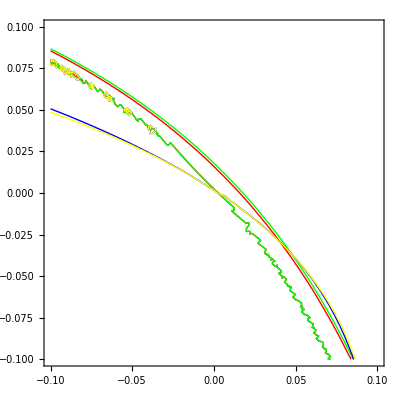

```mathematica
sa={c2->1/350.,d->5};
ContourPlot[{(eqf/.sa)==0,(eqz/.sa)==0,(eqcr/.sa)==-0.08,(eqla/.sa)==0.02,(eqpz/.sa)==-0.008},{c1,-0.1,0.1},{c3,-0.1,0.1},ContourStyle->{Red,Green,Blue,Yellow,Purple}]
```

```mathematica
sa={c2->1/350.,d->5.2};
ContourPlot[{(eqf/.sa)==0,(eqz/.sa)==0,(eqcr/.sa)==-0.05},{c1,-0.1,0.1},{c3,-0.1,0.1},ContourStyle->{Red,Green,Blue}]
```

### Valori approssimati

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick={3.5,4,1.5,7,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.65,4,2,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
sol1=FindRoot[{foc[1]==52,zog1[1,n]==40,zog1[2,n]-zog1[3,n]==-0.05},{c1,0.05},{c2,1/350},{c3,-0.05}]
```

### Si determinano tutti i raggi.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={3,4,1.5,7.2,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5,4,2,-Infinity,y1,22.6,{λ1,λ2,λ3}]
```

```mathematica
NSolve[{foc[1]==52,zog1[1,n]==42,zog1[2,n]-zog1[3,n]==0,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.05},{c1,0.05},{c2,1/350},{c3,-0.05},{c4,0.05},{c5,-1/350},{c6,-0.05},MaxIterations->300]
```

```mathematica
solf=FindRoot[{foc[1]==52,zog1[1,n]==42,zog1[2,n]-zog1[3,n]==-0.03,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.05},{c1,0.05},{c2,1/350},{c3,-0.05},{c4,0.05},{c5,-1/350},{c6,-0.05},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

### Si determinano tutti i raggi.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick={0,0,1.5,7.2,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5,4,2,-Infinity,y1,22.6,{λ1,λ2,λ3}]
```

```mathematica
NSolve[{Chop[foc[1]]==52,Chop[zog1[1,n]]==42,Chop[zog1[2,n]-zog1[3,n]]==0},{c1,c2,c3}]
```

$Aborted

```mathematica
solf=FindRoot[{foc[1]==52,zog1[1,n]==42,zog1[2,n]-zog1[3,n]==-0.03,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.05},{c1,0.05},{c2,1/350},{c3,-0.05},{c4,0.05},{c5,-1/350},{c6,-0.05},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

## Progetto del tripletto di Cooke (LaFN21-SF53-LaFN21)F/5-80mm (occorre cambiare i vetri)

### Si determina la forma (ϕ_i =c_i-c_(i+1)) delle tre lenti imponendo la focale, il cromatismo assiale e quello di ingrandimento per spessori nulli. Quest'ultima ipotesi è necessaria per avere relazioni gaussiane in cui intervengono soltanto le ϕ_i e non le c_i.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/(c1-ϕ1),1/c3,1/(c3-ϕ2),1/c5,1/(c5-ϕ3)};
thick={0,5,0,10,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},8,4,3,-Infinity,y1,15,{λ1,λ2,λ3}]
```

Si osservi che, per spessori nulli, le condizioni di focale assegnata, cromatismo assiale e cromatismo d'ingrandimento dipendono da ϕ1,ϕ2 e ϕ3 ma contengono termini piccolissimi dipendenti da c1,c2,c3.  Applicando il comando Chop questi termini si elidono ottenendosi relazioni che fornicono valori approssimati di ϕ1,ϕ2 e ϕ3.

```mathematica
eqf1=Chop[1/foc[1]-(1/80)];
eqz1=Chop[zog1[2,n]-zog1[3,n]];
eqla1=Chop[hobj1[2,n]-hobj1[3,n]];
```

### Per determinare i valori approssimati di ϕ1, ϕ2, ϕ3 mediante il comando FindRoot, si inizia con la rappresentazione grafica delle funzioni implicitamente definite eqf1=0, eqz1=0 e eqla1=0, fissando ad arbitrio un valore ragionevole di ϕ3. Questo studio grafico mostra che per valori negativi di ϕ3 si ottengono valori non accettabili per le altre due incognite.

```mathematica
so={ϕ3->-0.01};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

```mathematica
so={ϕ3->-0.005};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

```mathematica
so={ϕ3->0.02};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

```mathematica
so={ϕ3->0.01};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.08,(eqla1/.so)==0.05,Chop[zog1[1,n]]==42},{ϕ1,0.001,0.06},{ϕ2,-0.07,-0.01}]
```

### Valori approssimati

```mathematica
sol1=FindRoot[{eqf1==0,eqz1==-0.08,eqla1==0.05},{ϕ1,0.02},{ϕ2,-0.02},{ϕ3,0.01}]
```

### Si introducono gli spessori delle lenti lasciando invariati i valori di ϕ1, ϕ2, ϕ3 trovati in sol1. Quindi si determinano c1, c2, c3 imponendo la conservazione della focale e richiedendo l'eliminazione dell'aberrazione sferica e del coma.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/(c1-sol1[[1,2]]),1/c3,1/(c3-sol1[[2,2]]),1/c5,1/(c5-sol1[[3,2]])};
thick={0,5,0,10,0};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},10,4,3,-Infinity,y1,10,{λ1,λ2,λ3}]
```

### Analisi grafica per determinare valori approssimati delle curvature c1, c3, c5. Si osservi che le curve di colore grigio si riferiscono all'astigmatismo, quelle azzurre all'aberrazione sferica e quella viola al coma. I grafici sono ottenuti fissando il valore di c5. E' facile verificare che le tre curve non si incontrano in uno stesso punto al variare di c5. Inoltre, riducendo il valore di c5 aumentano quelli di c1 e c3. Pertanto si fissa un valore c5=0.02.

```mathematica
s1={c5->-0.015};
ContourPlot[{(Absftot[1]/.s1)==-0.01,(Comatot[1]/.s1)==0.002,(Asttot[1]/.s1)==0.02},{c1,0.01,0.07},{c3,-0.05,-0.01}]
```

```mathematica
s1={c5->0.002};
ContourPlot[{(Absftot[1]/.s1)==-0.01,(Comatot[1]/.s1)==0.002,(Asttot[1]/.s1)==0.02},{c1,0.01,0.07},{c3,-0.05,-0.01}]
```

### Individuati graficamente dei valori approssimati di c1, c3, c5, si prova a determinare quelli esatti con il comando FindRoot imponendo l'eliminazione dell'aberrazione sferica, del coma ed il mantenimento della focale.

```mathematica
solp=FindRoot[{Absftot[1]==-0.02,Comatot[1]==0.002,foc[1]==52},{c1,-0.01},{c3,-0.02},{c5,-0.01}]
```

```mathematica
solp=FindRoot[{Absftot[1]==-0.02,Comatot[1]==0.002,zog1[1,n]==42},{c1,0.02},{c3,-0.03},{c5,0.002}]
```

### Si assumono incognite tutte le curvature c1,c2, c3, c4, c5,c6 in modo da soddisfare le condizioni: focale assegnata, cromatismo assiale, cromatismo di ingrandimento, aberrazione sferica, coma e astigmatismo. Come dato di partenza per c6 si assume il valore c5 - ϕ1, con c5 dato da solp[[3,2]] e ϕ1 dato da sol1[[3,2]].

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={3,4,2,7.2,3};
ind={{1,1.792537,1,1.734722,1,1.792537,1},{1,1.79992,1,1.746348,1,1.79992,1},{1,1.783314,1,1.72096,1,1.783314,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5,4,2,-Infinity,y1,22,{λ1,λ2,λ3},2]
```

```mathematica
eqz2=zog1[2,n]-zog1[3,n];
eqla2=hobj1[2,n]-hobj1[3,n];
solp[[3,2]]-sol1[[3,2]];
```

```mathematica
solf=FindRoot[{foc[1]==52,eqz2==-0.08,eqla2==0.05,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.03},{c1,solp[[1,2]]},{c2,solp[[1,2]]-sol1[[1,2]]},{c3,solp[[2,2]]},{c4,solp[[2,2]]-sol1[[2,2]]},{c5,solp[[3,2]]},{c6,solp[[3,2]]-sol1[[3,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

### Tentativi vari: Si osservi che riducendo l'astigmatismo cresce la curvatura di campo. D'altra parte, poiché il valore dell'angolo di campo ci pone al di fuori della teoria del terzo ordine, occorre fare in modo che l'astigmatismo del quinto ordine compensi quello del terzo a 0.7 del raggio

#### 1° tent.

```mathematica
solf=FindRoot[{foc[1]==52,eqz2==-0.08,eqla2==0.05,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.05},{c1,solp[[1,2]]},{c2,solp[[1,2]]-sol1[[1,2]]},{c3,solp[[2,2]]},{c4,solp[[2,2]]-sol1[[2,2]]},{c5,solp[[3,2]]},{c6,solp[[3,2]]-sol1[[3,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

#### 2° tent.

```mathematica
solf=FindRoot[{foc[1]==52,eqz2==-0.08,eqla2==0.05,Absftot[1]==-0.02,Comatot[1]==0.002,Asttot[1]==0.06},{c1,solp[[1,2]]},{c2,solp[[1,2]]-sol1[[1,2]]},{c3,solp[[2,2]]},{c4,solp[[2,2]]-sol1[[2,2]]},{c5,solp[[3,2]]},{c6,solp[[3,2]]-sol1[[3,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r1 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

## Tripletto Oslo (SK16-F4-SK16) Si parte da un progetto simmetrico

### Si parte da un progetto simmetrico rispetto al diaframma con lenti a spessore non nullo in modo da avere tre soli raggi di curvatura a partire dai quali si impongono le condizioni di focale assegnata, cromatismo assiale e cromatismo di ingrandimento.

```mathematica
rad={1/c1,1/c2,1/c3,-1/c3,-1/c2,-1/c1};
thick={2,6,1,6,2};
ind={{1,1.62041,1,1.616592,1,1.62041,1},{1,1.627557,1,1.628480,1,1.627557,1},{1,1.617272,1,1.611645,1,1.617272,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.25,4,0.1,-Infinity,y1,22,{0.58,λ2,λ3}]
```

```mathematica
eqf1=foc[1]-52;
eqz1=zog1[2,n]-zog1[3,n];
eqla1=hobj1inf[2,n]-hobj1inf[3,n];
```

### Per determinare i valori approssimati di c1, c2, c3 , si inizia con la rappresentazione grafica delle funzioni implicitamente definite eqf1=0, eqz1=-0.1 e eqla1=0.025, fissando ad arbitrio un valore ragionevole di c2. Questo studio grafico mostra che per valori negativi di c2 si ottengono valori accettabili per le altre due incognite.

```mathematica
-1/160.
```

```mathematica
so={c2->-0.0063};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==-0.1,(eqla1/.so)==0.025},{c1,0,0.1},{c3,-0.1,0}]
```

### Valori approssimati

```mathematica
1/21.
```

```mathematica
sol1={c1->0.050,c2->-0.0063,c3->-0.049}; (* per conservare quanto più possibile la simmetria *)
eqf1[[1]]/.sol1
eqz1/.sol1
eqla1/.sol1
```

### Quindi si determinano c1, c2, c3 imponendo la conservazione della focale e richiedendo l'eliminazione dell'aberrazione sferica, del coma e dell'astigmatismo.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={2,6,1,6,2};
ind={{1,1.62041,1,1.616592,1,1.62041,1},{1,1.627557,1,1.628480,1,1.627557,1},{1,1.617272,1,1.611645,1,1.617272,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.25,4,0.5,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
solf=FindRoot[{foc[1]==52,eqz1==-0.08,eqla1==0.018,Absftot[1]==-0.04,Comatot[1]==-0.002,Asttot[1]==0.062},{c1,sol1[[1,2]]},{c2,sol1[[2,2]]},{c3,sol1[[3,2]]},{c4,-sol1[[3,2]]},{c5,-sol1[[2,2]]},{c6,-sol1[[1,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r6 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```

## Tripletto Oslo (SK16-F4-SK16) Si parte da un progetto simmetrico

### Si parte da un progetto simmetrico rispetto al diaframma con lenti a spessore non nullo in modo da avere tre soli raggi di curvatura a partire dai quali si impongono le condizioni di focale assegnata, cromatismo assiale e cromatismo di ingrandimento.

```mathematica
rad={1/c1,1/c2,1/c2,1/c4};
thick={8,0.5,17.19};
index={{1,1.56081792,1,1.4879367,1},{1,1.5655173,1,1.49055758,1},{1,1.55520714,1,1.4847972,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0},50,0,0,-Infinity,y1,0.4,{0.58,λ2,λ3}]
```

```mathematica
eqf1=foc[1]-1000;
eqz1=zog1[2,n]-zog1[3,n];
eqla1=hobj1inf[2,n]-hobj1inf[3,n];
```

### Per determinare i valori approssimati di c1, c2, c3 , si inizia con la rappresentazione grafica delle funzioni implicitamente definite eqf1=0, eqz1=-0.1 e eqla1=0.025, fissando ad arbitrio un valore ragionevole di c2. Questo studio grafico mostra che per valori negativi di c2 si ottengono valori accettabili per le altre due incognite.

```mathematica
so={c4->-0.00002};
ContourPlot[{(eqf1/.so)==0,(eqz1/.so)==0,(eqla1/.so)==0},{c1,0,0.01},{c2,-0.01,0}]
```

### Valori approssimati

```mathematica
1/21.
```

```mathematica
sol1={c1->0.050,c2->-0.0063,c3->-0.049}; (* per conservare quanto più possibile la simmetria *)
eqf1[[1]]/.sol1
eqz1/.sol1
eqla1/.sol1
```

### Quindi si determinano c1, c2, c3 imponendo la conservazione della focale e richiedendo l'eliminazione dell'aberrazione sferica, del coma e dell'astigmatismo.

```mathematica
(* tripletto con vetri LaFN21, SF53, LaFN21*)
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={2,6,1,6,2};
ind={{1,1.62041,1,1.616592,1,1.62041,1},{1,1.627557,1,1.628480,1,1.627557,1},{1,1.617272,1,1.611645,1,1.617272,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},5.25,4,0.5,-Infinity,y1,22,{λ1,λ2,λ3}]
```

```mathematica
solf=FindRoot[{foc[1]==52,eqz1==-0.08,eqla1==0.018,Absftot[1]==-0.04,Comatot[1]==-0.002,Asttot[1]==0.062},{c1,sol1[[1,2]]},{c2,sol1[[2,2]]},{c3,sol1[[3,2]]},{c4,-sol1[[3,2]]},{c5,-sol1[[2,2]]},{c6,-sol1[[1,2]]},MaxIterations->300]
```

```mathematica
Print["r1 = ",1/solf[[1,2]]]
Print["r2 = ",1/solf[[2,2]]]
Print["r3 = ",1/solf[[3,2]]]
Print["r4 = ",1/solf[[4,2]]]
Print["r5 = ",1/solf[[5,2]]]
Print["r6 = ",1/solf[[6,2]]]
Print["f = ",foc[1]/.solf]
Print["back foc. = ",zog1[1,n]/.solf]
Print["Δf = ",(zog1[2,n]-zog1[3,n])/.solf]
Print["Δh = ",(hobj1inf[2,n]-hobj1inf[3,n])/.solf]
Print["ab. sf. = ",Absftot[1]/.solf]
Print["coma = ",Comatot[1]/.solf]
Print["ast = ",Asttot[1]/.solf]
Print["curv. = ",Curvtot[1]/.solf]
Print["raggio petz. = ",Petzval[1]/.solf]
```